## Well-Tempered Minkowski vacuum in Teleparallel Horndeski theory

This notebook studies well-tempered Minkowski solutions in the Teleparallel analogue of Horndeski gravity (for short, Teledeski). See arXiv:2108.02500 for more details and email any time for questions.

Please cite arXiv:2108.02500 if this notebook was in any way helpful. Thank you. Best regards, - Reggie

### I. Teledeski: Cosmology

This section provides the modified Friedmann equations and the scalar field equation in Teledeski. For the full details of its derivation, we refer the reader to the other notebook TeleDeski GW Propagation Equation [Without L5].nb.

The Lagrangian terms are given by...

```mathematica
bg={NN->Function[t,1],aa->Function[t,a[t]],T->(6 a'[t]^2)/a[t]^2,B->(6 (2 a'[t]^2+a[t] a''[t]))/a[t]^2,XX->1/2 ϕ'[t]^2,II2->(3 a'[t] ϕ'[t])/a[t],TVec->-(9 a'[t]^2)/a[t]^2};
ℒ2=aa[t]^3 G2[ϕ[t],ϕ'[t]^2/(2 NN[t]^2)] NN[t]/.bg;
ℒ3=1/NN[t]^2 aa[t]^2 G3[ϕ[t],ϕ'[t]^2/(2 NN[t]^2)] (-aa[t] NN'[t] ϕ'[t]+NN[t] (3 aa'[t] ϕ'[t]+aa[t] ϕ''[t]))/.bg;
ℒ4=1/NN[t]^4 6 aa[t] (G4[ϕ[t],ϕ'[t]^2/(2 NN[t]^2)] NN[t]^2 (-aa[t] aa'[t] NN'[t]+NN[t] (aa'[t]^2+aa[t] aa''[t]))+aa'[t] ϕ'[t] (-aa[t] NN'[t] ϕ'[t]+NN[t] (aa'[t] ϕ'[t]+aa[t] ϕ''[t])) Derivative[0,1][G4][ϕ[t],ϕ'[t]^2/(2 NN[t]^2)])/.bg;
ℒTele=aa[t]^3 GTele[ϕ[t],ϕ'[t]^2/(2 NN[t]^2),(6 aa'[t]^2)/(aa[t]^2 NN[t]^2),0,-(9 aa'[t]^2)/(aa[t]^2 NN[t]^2),(3 aa'[t] ϕ'[t])/(aa[t] NN[t]^2),0,0,0,0,0,0] NN[t]/.bg;
```

The functional derivatives of these lead to the field equations. The Friedmann equations are given by...

```mathematica
Feqℒ2=aa[t]^3 (G2[ϕ[t],XX]-ϕ'[t]^2 Derivative[0,1][G2][ϕ[t],XX])/.bg;
Feqℒ3=aa[t]^2 ϕ'[t]^2 (-3 aa'[t] ϕ'[t] Derivative[0,1][G3][ϕ[t],XX]+aa[t] Derivative[1,0][G3][ϕ[t],XX])/.bg;
Feqℒ4=6 aa[t] aa'[t] (G4[ϕ[t],XX] aa'[t]+ϕ'[t] (-aa'[t] (2 ϕ'[t] Derivative[0,1][G4][ϕ[t],XX]+ϕ'[t]^3 Derivative[0,2][G4][ϕ[t],XX])+aa[t] (Derivative[1,0][G4][ϕ[t],XX]+ϕ'[t]^2 Derivative[1,1][G4][ϕ[t],XX])))/.bg;
FeqℒTele=aa[t] (-6 aa[t] aa'[t] ϕ'[t] Derivative[0,0,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+6 aa'[t]^2 (3 Derivative[0,0,0,0,1,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-2 Derivative[0,0,1,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])+aa[t]^2 (GTele[ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-ϕ'[t]^2 Derivative[0,1,0,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]))/.bg;


Peqℒ2=3 aa[t]^2 G2[ϕ[t],XX]/.bg;
Peqℒ3=-3 aa[t]^2 ϕ'[t]^2 (ϕ''[t] Derivative[0,1][G3][ϕ[t],XX]+Derivative[1,0][G3][ϕ[t],XX])/.bg;
Peqℒ4=6 (G4[ϕ[t],XX] (aa'[t]^2+2 aa[t] aa''[t])-aa'[t]^2 ϕ'[t]^2 Derivative[0,1][G4][ϕ[t],XX]-2 aa[t] aa'[t] ϕ'[t] (ϕ''[t] (Derivative[0,1][G4][ϕ[t],XX]+ϕ'[t]^2 Derivative[0,2][G4][ϕ[t],XX])-Derivative[1,0][G4][ϕ[t],XX]+ϕ'[t]^2 Derivative[1,1][G4][ϕ[t],XX])+aa[t] (aa[t] ϕ''[t] Derivative[1,0][G4][ϕ[t],XX]+ϕ'[t]^2 (-2 aa''[t] Derivative[0,1][G4][ϕ[t],XX]+aa[t] (ϕ''[t] Derivative[1,1][G4][ϕ[t],XX]+Derivative[2,0][G4][ϕ[t],XX]))))/.bg;
PeqℒTele=-1/aa[t]^2 3 (aa[t]^2 aa'[t] (12 ϕ'[t] aa''[t] (-3 Derivative[0,0,0,0,1,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+2 Derivative[0,0,1,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])+aa'[t] (-3 ϕ'[t]^2 Derivative[0,0,0,0,0,2,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+2 (-6 Derivative[0,0,0,0,1,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-9 ϕ''[t] Derivative[0,0,0,0,1,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+4 Derivative[0,0,1,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+6 ϕ''[t] Derivative[0,0,1,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])))-12 aa'[t]^4 (9 Derivative[0,0,0,0,2,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+4 (-3 Derivative[0,0,1,0,1,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+Derivative[0,0,2,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]))+12 aa[t] aa'[t]^2 (aa'[t] ϕ'[t] (3 Derivative[0,0,0,0,1,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-2 Derivative[0,0,1,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])+aa''[t] (9 Derivative[0,0,0,0,2,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+4 (-3 Derivative[0,0,1,0,1,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+Derivative[0,0,2,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])))+aa[t]^4 (-GTele[ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+ϕ''[t] (Derivative[0,0,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+ϕ'[t]^2 Derivative[0,1,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])+ϕ'[t]^2 Derivative[1,0,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])+aa[t]^3 (aa''[t] (3 ϕ'[t]^2 Derivative[0,0,0,0,0,2,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-6 Derivative[0,0,0,0,1,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+4 Derivative[0,0,1,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])+aa'[t] ϕ'[t] (3 Derivative[0,0,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+ϕ''[t] (3 Derivative[0,0,0,0,0,2,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-6 Derivative[0,1,0,0,1,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+4 Derivative[0,1,1,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])-6 Derivative[1,0,0,0,1,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+4 Derivative[1,0,1,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])))/.bg;

Feq=Feqℒ2+Feqℒ3+Feqℒ4+FeqℒTele;
Peq=Peqℒ2+Peqℒ3+Peqℒ4+PeqℒTele;
```

The scalar field equation is given by...

```mathematica
Seqℒ2=aa[t]^2 (-3 aa'[t] ϕ'[t] Derivative[0,1][G2][ϕ[t],XX]-aa[t] (ϕ''[t] (Derivative[0,1][G2][ϕ[t],XX]+ϕ'[t]^2 Derivative[0,2][G2][ϕ[t],XX])-Derivative[1,0][G2][ϕ[t],XX]+ϕ'[t]^2 Derivative[1,1][G2][ϕ[t],XX]))/.bg;
Seqℒ3=aa[t] (-6 aa'[t]^2 ϕ'[t]^2 Derivative[0,1][G3][ϕ[t],XX]-3 aa[t] aa'[t] ϕ'[t] (ϕ''[t] (2 Derivative[0,1][G3][ϕ[t],XX]+ϕ'[t]^2 Derivative[0,2][G3][ϕ[t],XX])-2 Derivative[1,0][G3][ϕ[t],XX]+ϕ'[t]^2 Derivative[1,1][G3][ϕ[t],XX])+aa[t] (2 aa[t] ϕ''[t] Derivative[1,0][G3][ϕ[t],XX]+ϕ'[t]^2 (-3 aa''[t] Derivative[0,1][G3][ϕ[t],XX]+aa[t] (ϕ''[t] Derivative[1,1][G3][ϕ[t],XX]+Derivative[2,0][G3][ϕ[t],XX]))))/.bg;
Seqℒ4=6 (-aa'[t]^3 ϕ'[t] (Derivative[0,1][G4][ϕ[t],XX]+ϕ'[t]^2 Derivative[0,2][G4][ϕ[t],XX])+aa[t]^2 aa''[t] (Derivative[1,0][G4][ϕ[t],XX]+ϕ'[t]^2 Derivative[1,1][G4][ϕ[t],XX])-aa[t] aa'[t]^2 (ϕ''[t] (Derivative[0,1][G4][ϕ[t],XX]+4 ϕ'[t]^2 Derivative[0,2][G4][ϕ[t],XX]+ϕ'[t]^4 Derivative[0,3][G4][ϕ[t],XX])-Derivative[1,0][G4][ϕ[t],XX]-2 ϕ'[t]^2 Derivative[1,1][G4][ϕ[t],XX]+ϕ'[t]^4 Derivative[1,2][G4][ϕ[t],XX])+aa[t] aa'[t] ϕ'[t] (-2 aa''[t] (Derivative[0,1][G4][ϕ[t],XX]+ϕ'[t]^2 Derivative[0,2][G4][ϕ[t],XX])+aa[t] (ϕ''[t] (3 Derivative[1,1][G4][ϕ[t],XX]+ϕ'[t]^2 Derivative[1,2][G4][ϕ[t],XX])+ϕ'[t]^2 Derivative[2,1][G4][ϕ[t],XX])))/.bg;
SeqℒTele=3 aa[t] aa'[t]^2 Derivative[0,0,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-3 aa[t]^2 aa''[t] Derivative[0,0,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-aa[t]^3 ϕ''[t] Derivative[0,1,0,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-3 aa[t] aa'[t] (3 aa'[t] Derivative[0,0,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+aa[t] ϕ'[t] Derivative[0,1,0,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])+aa[t]^3 Derivative[1,0,0,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+1/aa[t] 3 aa'[t] (-3 aa[t] (-aa'[t]^2 ϕ'[t]+aa[t] ϕ'[t] aa''[t]+aa[t] aa'[t] ϕ''[t]) Derivative[0,0,0,0,0,2,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-18 aa'[t] (aa'[t]^2-aa[t] aa''[t]) Derivative[0,0,0,0,1,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+12 aa'[t] (aa'[t]^2-aa[t] aa''[t]) Derivative[0,0,1,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-aa[t]^3 ϕ'[t] ϕ''[t] Derivative[0,1,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-aa[t]^3 ϕ'[t] Derivative[1,0,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])+ϕ'[t] (-3 aa[t] (-aa'[t]^2 ϕ'[t]+aa[t] ϕ'[t] aa''[t]+aa[t] aa'[t] ϕ''[t]) Derivative[0,1,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-18 aa'[t] (aa'[t]^2-aa[t] aa''[t]) Derivative[0,1,0,0,1,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+12 aa'[t] (aa'[t]^2-aa[t] aa''[t]) Derivative[0,1,1,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-aa[t]^3 ϕ'[t] ϕ''[t] Derivative[0,2,0,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-aa[t]^3 ϕ'[t] Derivative[1,1,0,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])/.bg;
```

These field equations propel us to well-tempered cosmology.

### II. The Well-Tempered Minkowski Recipe: H(t)→0

We set the ingredients necessary to admit Minkowski solutions in Teledeski gravity.

We focus on the shift symmetric sector; in which case we rewrite the Horndeski and Teledeski potential as...

```mathematica
GTeleTo𝒢=GTele->Function[{a,b,c,d,e,f,g,h,i,j,k,l},𝒢[b,c,f]];

SS={G2->Function[{ϕ,X},V[X]-λ^3 ϕ],G3->Function[{ϕ,X},G[X]],G4->Function[{ϕ,X},κ+(M ϕ+A[X])/2]};
```

The cosmological field equations (with the matter source term) are now given by...

```mathematica
SimpColl[expr_]:=Collect[expr,{κ,V[x_],Derivative[u_][V][x_],G[x_],Derivative[u_][G][x_],𝒢[b_,c_,f_],Derivative[B_,C_,F_][𝒢][b_,c_,f_],ρ[t_],P[t_]},Simplify]

$Assumptions=a[t]>0;
aToH=Solve[{H[t]==a'[t]/a[t],H'[t]==D[(a'[t]/a[t]), t]},{a'[t],a''[t]}][[1]];

FeqM=-a[t]^3 ρ[t];
PeqM=3 a[t]^2 P[t];

FeqTH=SimpColl[(Feqℒ2+Feqℒ3+Feqℒ4+FeqℒTele+FeqM/.GTeleTo𝒢/.SS/.aToH)]==0;
PeqTH=SimpColl[Peqℒ2+Peqℒ3+Peqℒ4+PeqℒTele+PeqM/.GTeleTo𝒢/.SS/.aToH]==0;
SeqTH=SimpColl[Seqℒ2+Seqℒ3+Seqℒ4+SeqℒTele/.GTeleTo𝒢/.SS/.aToH]==0;

FeqTH
PeqTH
SeqTH
```

6 κ a[t]^3 H[t]^2+a[t]^3 V[1/2 ϕ'[t]^2]+a[t]^3 𝒢[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-a[t]^3 ρ[t]-a[t]^3 V'[1/2 ϕ'[t]^2] ϕ'[t]^2-3 a[t]^3 H[t] G'[1/2 ϕ'[t]^2] ϕ'[t]^3-a[t]^3 (-3 A[1/2 ϕ'[t]^2] H[t]^2+(λ^3-3 M H[t]^2) ϕ[t]+3 H[t] ϕ'[t] (-M+2 H[t] A'[1/2 ϕ'[t]^2] ϕ'[t]+H[t] ϕ'[t]^3 A''[1/2 ϕ'[t]^2]))-6 a[t]^3 H[t] ϕ'[t] 𝒢^(0,0,1)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-12 a[t]^3 H[t]^2 𝒢^(0,1,0)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-a[t]^3 ϕ'[t]^2 𝒢^(1,0,0)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]==0

3 a[t]^2 P[t]+3 a[t]^2 V[1/2 ϕ'[t]^2]+3 a[t]^2 𝒢[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]+6 κ a[t]^2 (3 H[t]^2+2 H'[t])-3 a[t]^2 G'[1/2 ϕ'[t]^2] ϕ'[t]^2 ϕ''[t]+3 a[t]^2 (A[1/2 ϕ'[t]^2] (3 H[t]^2+2 H'[t])+ϕ[t] (-λ^3+3 M H[t]^2+2 M H'[t])+2 M H[t] ϕ'[t]-3 H[t]^2 A'[1/2 ϕ'[t]^2] ϕ'[t]^2-2 A'[1/2 ϕ'[t]^2] H'[t] ϕ'[t]^2+M ϕ''[t]-2 H[t] A'[1/2 ϕ'[t]^2] ϕ'[t] ϕ''[t]-2 H[t] ϕ'[t]^3 A''[1/2 ϕ'[t]^2] ϕ''[t])-3 a[t]^2 (3 H[t] ϕ'[t]+ϕ''[t]) 𝒢^(0,0,1)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-9 a[t]^2 ϕ'[t] (H'[t] ϕ'[t]+H[t] ϕ''[t]) 𝒢^(0,0,2)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-12 a[t]^2 (3 H[t]^2+H'[t]) 𝒢^(0,1,0)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-36 a[t]^2 H[t] (2 H'[t] ϕ'[t]+H[t] ϕ''[t]) 𝒢^(0,1,1)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-144 a[t]^2 H[t]^2 H'[t] 𝒢^(0,2,0)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-3 a[t]^2 ϕ'[t]^2 ϕ''[t] 𝒢^(1,0,1)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-12 a[t]^2 H[t] ϕ'[t] ϕ''[t] 𝒢^(1,1,0)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]==0

-3 a[t]^3 H[t] ϕ'[t]^3 G''[1/2 ϕ'[t]^2] ϕ''[t]-a[t]^3 ϕ'[t]^2 V''[1/2 ϕ'[t]^2] ϕ''[t]-a[t]^3 V'[1/2 ϕ'[t]^2] (3 H[t] ϕ'[t]+ϕ''[t])-3 a[t]^3 G'[1/2 ϕ'[t]^2] ϕ'[t] (3 H[t]^2 ϕ'[t]+H'[t] ϕ'[t]+2 H[t] ϕ''[t])-a[t]^3 (λ^3-3 M H'[t]+9 H[t]^3 ϕ'[t] (A'[1/2 ϕ'[t]^2]+ϕ'[t]^2 A''[1/2 ϕ'[t]^2])+6 H[t] H'[t] ϕ'[t] (A'[1/2 ϕ'[t]^2]+ϕ'[t]^2 A''[1/2 ϕ'[t]^2])+3 H[t]^2 (-2 M+A'[1/2 ϕ'[t]^2] ϕ''[t]+4 ϕ'[t]^2 A''[1/2 ϕ'[t]^2] ϕ''[t]+ϕ'[t]^4 ϕ''[t] A^(3)[1/2 ϕ'[t]^2]))-3 a[t]^3 (3 H[t]^2+H'[t]) 𝒢^(0,0,1)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-9 a[t]^3 H[t] (H'[t] ϕ'[t]+H[t] ϕ''[t]) 𝒢^(0,0,2)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-36 a[t]^3 H[t]^2 H'[t] 𝒢^(0,1,1)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-a[t]^3 (3 H[t] ϕ'[t]+ϕ''[t]) 𝒢^(1,0,0)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-3 a[t]^3 ϕ'[t] (H'[t] ϕ'[t]+2 H[t] ϕ''[t]) 𝒢^(1,0,1)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-12 a[t]^3 H[t] H'[t] ϕ'[t] 𝒢^(1,1,0)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-a[t]^3 ϕ'[t]^2 ϕ''[t] 𝒢^(2,0,0)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]==0

The Hubble equation is given by...

```mathematica
HeqTH=SimpColl[PeqTH[[1]]-PeqTH[[2]]/.κ->kHsq/H[t]^2/.Solve[FeqTH/.κ->kHsq/H[t]^2,kHsq][[1]]/.Solve[FeqTH,V[ϕ'[t]^2/2]][[1]]]==0;

HeqTH
```

3 a[t]^2 P[t]+3 a[t]^2 ρ[t]+12 κ a[t]^2 H'[t]+3 a[t]^2 V'[1/2 ϕ'[t]^2] ϕ'[t]^2+3 a[t]^2 G'[1/2 ϕ'[t]^2] ϕ'[t]^2 (3 H[t] ϕ'[t]-ϕ''[t])+3 a[t]^2 (2 A[1/2 ϕ'[t]^2] H'[t]+2 M ϕ[t] H'[t]-M H[t] ϕ'[t]+3 H[t]^2 A'[1/2 ϕ'[t]^2] ϕ'[t]^2-2 A'[1/2 ϕ'[t]^2] H'[t] ϕ'[t]^2+3 H[t]^2 ϕ'[t]^4 A''[1/2 ϕ'[t]^2]+M ϕ''[t]-2 H[t] A'[1/2 ϕ'[t]^2] ϕ'[t] ϕ''[t]-2 H[t] ϕ'[t]^3 A''[1/2 ϕ'[t]^2] ϕ''[t])+3 a[t]^2 (3 H[t] ϕ'[t]-ϕ''[t]) 𝒢^(0,0,1)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-9 a[t]^2 ϕ'[t] (H'[t] ϕ'[t]+H[t] ϕ''[t]) 𝒢^(0,0,2)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-12 a[t]^2 H'[t] 𝒢^(0,1,0)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-36 a[t]^2 H[t] (2 H'[t] ϕ'[t]+H[t] ϕ''[t]) 𝒢^(0,1,1)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-144 a[t]^2 H[t]^2 H'[t] 𝒢^(0,2,0)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]+3 a[t]^2 ϕ'[t]^2 𝒢^(1,0,0)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-3 a[t]^2 ϕ'[t]^2 ϕ''[t] 𝒢^(1,0,1)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]-12 a[t]^2 H[t] ϕ'[t] ϕ''[t] 𝒢^(1,1,0)[1/2 ϕ'[t]^2,6 H[t]^2,3 H[t] ϕ'[t]]==0

The degeneracy equation allowing Minkowski solutions can be obtained by taking the H(t)→0. This limit over-constrains the dynamical system and well-tempering resolves this by adjusting the field ϕ(t) in the degenerate space of the dynamical equations.

To get there, we first obtain the Minkowski vacuum limits of the background field equations...

```mathematica
MVac={H->Function[t,0],ρ[t]->Λ,P[t]->-Λ};

FeqTHMVac=SimpColl[FeqTH[[1]]/a[t]^3/.MVac]==0;
PeqTHMVac=SimpColl[PeqTH[[1]]/a[t]^2/.MVac]==0;
HeqTHMVac=SimpColl[HeqTH[[1]]/a[t]^2/.MVac]==0;
SeqTHMVac=SimpColl[SeqTH[[1]]/a[t]^3/.MVac]==0;

FeqTHMVac
PeqTHMVac
HeqTHMVac
SeqTHMVac
```

-Λ+V[1/2 ϕ'[t]^2]+𝒢[1/2 ϕ'[t]^2,0,0]-λ^3 ϕ[t]-V'[1/2 ϕ'[t]^2] ϕ'[t]^2-ϕ'[t]^2 𝒢^(1,0,0)[1/2 ϕ'[t]^2,0,0]==0

3 V[1/2 ϕ'[t]^2]+3 𝒢[1/2 ϕ'[t]^2,0,0]-3 G'[1/2 ϕ'[t]^2] ϕ'[t]^2 ϕ''[t]-3 (Λ+λ^3 ϕ[t]-M ϕ''[t])-3 ϕ''[t] 𝒢^(0,0,1)[1/2 ϕ'[t]^2,0,0]-3 ϕ'[t]^2 ϕ''[t] 𝒢^(1,0,1)[1/2 ϕ'[t]^2,0,0]==0

3 V'[1/2 ϕ'[t]^2] ϕ'[t]^2+3 M ϕ''[t]-3 G'[1/2 ϕ'[t]^2] ϕ'[t]^2 ϕ''[t]-3 ϕ''[t] 𝒢^(0,0,1)[1/2 ϕ'[t]^2,0,0]+3 ϕ'[t]^2 𝒢^(1,0,0)[1/2 ϕ'[t]^2,0,0]-3 ϕ'[t]^2 ϕ''[t] 𝒢^(1,0,1)[1/2 ϕ'[t]^2,0,0]==0

-λ^3-V'[1/2 ϕ'[t]^2] ϕ''[t]-ϕ'[t]^2 V''[1/2 ϕ'[t]^2] ϕ''[t]-ϕ''[t] 𝒢^(1,0,0)[1/2 ϕ'[t]^2,0,0]-ϕ'[t]^2 ϕ''[t] 𝒢^(2,0,0)[1/2 ϕ'[t]^2,0,0]==0

These are the generalizations to Eqs. (2.4-7) in 2009.01723 (Fugue in B Flat). The well-tempered degeneracy equation can be obtained by matching the coefficients of ϕ^(..) in the Hubble and scalar field equations...

```mathematica
𝒴=Coefficient[HeqTHMVac[[1]],ϕ''[t],0];
𝒵=Coefficient[HeqTHMVac[[1]],ϕ''[t],1];
𝒞=Coefficient[SeqTHMVac[[1]],ϕ''[t],0];
𝒟=Coefficient[SeqTHMVac[[1]],ϕ''[t],1];

ϕTox=Solve[{x[t]==ϕ'[t]^2/2,x'[t]==D[(ϕ'[t]^2/2), t]},{ϕ'[t],ϕ''[t]}][[2]];

DegeneracyEq=(𝒞 𝒵-𝒴 𝒟/.ϕTox/.x[t]->x//Simplify)==0;

DegeneracyEq
```

-3 λ^3 (M-2 x G'[x]-𝒢^(0,0,1)[x,0,0]-2 x 𝒢^(1,0,1)[x,0,0])+6 x (V'[x]+𝒢^(1,0,0)[x,0,0]) (V'[x]+2 x V''[x]+𝒢^(1,0,0)[x,0,0]+2 x 𝒢^(2,0,0)[x,0,0])==0

The general solution to this can be expressed as a braiding functional G[V(x),𝒢(x)]...

```mathematica
G3DegeneracySol=Solve[DegeneracyEq,G'[x]][[1]];

2x λ^3 G'[x]-(2x λ^3 G'[x]/.G3DegeneracySol//Simplify)==0//FullSimplify//TraditionalForm
```

λ^3 M==2 x ((𝒢^(1,0,0)(x,0,0)+V'(x)) (2 x (𝒢^(2,0,0)(x,0,0)+V''(x))+𝒢^(1,0,0)(x,0,0)+V'(x))+λ^3 𝒢^(1,0,1)(x,0,0))+λ^3 𝒢^(0,0,1)(x,0,0)+2 λ^3 x G'(x)

This is the generalization to Eqs. (3.3) [B Flat Minor] and (4.2) [B Flat Major] in 2009.01723. To see this, we can just take the appropriate Fugue Horndeski potentials...

```mathematica
FugueBFlatMinor={M->0,𝒢->Function[{X,T,I2},0]};
G'[x]==(G'[x]/.Solve[
DegeneracyEq/.FugueBFlatMinor,G'[x]][[1]])

FugueBFlatMajor={𝒢->Function[{X,T,I2},0]};
(λ3/(V'[x]+2 x V''[x])/.Solve[
DegeneracyEq/.FugueBFlatMajor/.λ^3->λ3,λ3][[1]]//Simplify)==λ^3/(V'[x]+2 x V''[x])
```

G'[x]==-(V'[x] (V'[x]+2 x V''[x]))/λ^3

(2 x V'[x])/(M-2 x G'[x])==λ^3/(V'[x]+2 x V''[x])

Obviously, these are Eqs. (3.3) and (4.2) of 2009.01723. We now look for the teleparallel gravity extensions to these Fugue functions.

### III. Fugue in B Flat [Extended Cut]

We obtain Teledeski models admitting a well-tempered Minkowski vacuum. We start with a short review of the Fugue models...

#### A. Fugue in B Flat Minor: G_3+K [review]

The B-flat minor limit is given by...

```mathematica
FugueBFlatMinor={M->0,𝒢->Function[{X,T,I2},0]};
```

The degeneracy equation becomes...

```mathematica
DegeneracyEqBFlatMinor=DegeneracyEq/.FugueBFlatMinor;DegeneracyEqBFlatMinor
```

6 x λ^3 G'[x]+6 x V'[x] (V'[x]+2 x V''[x])==0

We can find various solutions to this by substituting either V or G. The canonical kinetic term ansatz V(x)=ϵ X leads to...

```mathematica
BFlatMinorV1=V->Function[x,ϵ x];
BFlatMinorG1=DSolve[DegeneracyEqBFlatMinor/.BFlatMinorV1,G,x][[1]]/.C[1]->0;

V[x]==(V[x]/.BFlatMinorV1)
G[x]==(G[x]/.BFlatMinorG1)
```

V[x]==x ϵ

G[x]==-(x ϵ^2)/λ^3

The scalar solution and the Hamiltonian constraint becomes...

```mathematica
SeqTHMVac/.FugueBFlatMinor/.BFlatMinorV1/.BFlatMinorG1//Simplify
ϕ[t]==(ϕ[t]/.DSolve[%,ϕ,t][[1]])
FeqTHMVac/.FugueBFlatMinor/.BFlatMinorV1/.BFlatMinorG1/.DSolve[%%,ϕ,t][[1]]//Simplify
```

λ^3+ϵ ϕ''[t]==0

ϕ[t]==-(t^2 λ^3)/(2 ϵ)+C[1]+t C[2]

2 Λ+2 λ^3 C[1]+ϵ C[2]^2==0

This shows Λ is being tuned away by the dynamical scalar constants c_1 and c_2. Taking a power law kinetic term V'(x)=ϵ x^n we obtain...

```mathematica
BFlatMinorV2=DSolve[V'[x]==ϵ x^n,V,x][[1]]/.C[1]->0;
BFlatMinorG2=DSolve[DegeneracyEqBFlatMinor/.BFlatMinorV2,G,x][[1]]/.C[1]->0;

V[x]==(V[x]/.BFlatMinorV2)
G[x]==(G[x]/.BFlatMinorG2)
```

V[x]==(x^(1+n) ϵ)/(1+n)

G[x]==-(x^(1+2 n) ϵ^2)/λ^3

The scalar equation becomes...

```mathematica
SeqBFlatmV2G2=SeqTHMVac/.FugueBFlatMinor/.BFlatMinorV2/.BFlatMinorG2//Simplify;SeqBFlatmV2G2

ϕSolBFlatmV2G2=DSolve[SeqBFlatmV2G2,ϕ,t][[1]]//Simplify;

ϕ'[t]==(ϕ'[t]/.ϕSolBFlatmV2G2//Simplify)
```

2^n λ^3+(1+2 n) ϵ (ϕ'[t]^2)^n ϕ''[t]==0

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

ϕ'[t]==(-(2^n t λ^3)/ϵ+C[1]+2 n C[1])^(1/(1+2 n))

The Hamiltonian constraint can be confirmed to be Λ+λ^3 c_2 for this model...

```mathematica
(FeqTHMVac/.FugueBFlatMinor/.BFlatMinorV2/.BFlatMinorG2/.ϕSolBFlatmV2G2//FullSimplify)/.(2^n t λ^3-(1+2 n) ϵ C[1])->-ϵ(-(2^n t λ^3)/ϵ+C[1]+2 n C[1])/.(expr_^(2/(1+2n_)))^(1+n_):>expr^((2(1+n))/(1+2n))//Simplify
```

Λ+λ^3 C[2]==0

This shows that Λ is being tuned away by c_2 which characterizes the dynamics of the scalar.

#### B. Fugue in B Flat Major: G_4+G_3+K [review]

The B-flat major limit is...

```mathematica
FugueBFlatMajor={𝒢->Function[{X,T,I2},0]};
```

The degeneracy equation becomes...

```mathematica
DegeneracyEqBFlatMajor=DegeneracyEq/.FugueBFlatMajor;DegeneracyEqBFlatMajor
```

-3 λ^3 (M-2 x G'[x])+6 x V'[x] (V'[x]+2 x V''[x])==0

This can be played the same way as with the B Flat Minor case. For a canonical kinetic term ansatz V(x)=ϵ X, we obtain...

```mathematica
BFlatMajorV1=V->Function[x,ϵ x];
BFlatMajorG1=DSolve[DegeneracyEqBFlatMajor/.BFlatMajorV1,G,x][[1]]/.C[1]->0;

V[x]==(V[x]/.BFlatMajorV1)
G[x]==(G[x]/.BFlatMajorG1)
```

V[x]==x ϵ

G[x]==-(x ϵ^2)/λ^3+1/2 M Log[x]

The scalar field and the Hamiltonian constraint becomes...

```mathematica
SeqTHMVac/.FugueBFlatMajor/.BFlatMajorV1/.BFlatMajorG1//Simplify
ϕ[t]==(ϕ[t]/.DSolve[%,ϕ,t][[1]])
FeqTHMVac/.FugueBFlatMajor/.BFlatMajorV1/.BFlatMajorG1/.DSolve[%,ϕ,t][[1]]//Simplify
```

λ^3+ϵ ϕ''[t]==0

ϕ[t]==-(t^2 λ^3)/(2 ϵ)+C[1]+t C[2]

2 Λ+2 λ^3 C[1]+ϵ C[2]^2==0

For a power law kinetic term ansatz, V'(x)=ϵ x^n, we obtain...

```mathematica
BFlatMajorV2=DSolve[V'[x]==ϵ x^n,V,x][[1]]/.C[1]->0;
BFlatMajorG2=DSolve[DegeneracyEqBFlatMajor/.BFlatMajorV2,G,x][[1]]/.C[1]->0;

V[x]==(V[x]/.BFlatMajorV2)
G[x]==(G[x]/.BFlatMajorG2//Expand)
```

V[x]==(x^(1+n) ϵ)/(1+n)

G[x]==-(x^(1+2 n) ϵ^2)/λ^3+1/2 M Log[x]

The scalar equation becomes...

```mathematica
SeqBFlatMV2G2=SeqTHMVac/.FugueBFlatMajor/.BFlatMajorV2/.BFlatMajorG2//Simplify;SeqBFlatMV2G2

ϕSolBFlatMV2G2=DSolve[SeqBFlatMV2G2,ϕ,t][[1]]/.C[1]->C[1]/(1+2n);

ϕ'[t]==(ϕ'[t]/.ϕSolBFlatMV2G2//Simplify)
```

2^n λ^3+(1+2 n) ϵ (ϕ'[t]^2)^n ϕ''[t]==0

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

ϕ'[t]==(-(2^n t λ^3)/ϵ+C[1])^(1/(1+2 n))

The Hamiltonian constraint can be confirmed to be Λ+λ^3 c_2 for this model...

```mathematica
(FeqTHMVac/.FugueBFlatMajor/.BFlatMajorV2/.BFlatMajorG2/.ϕSolBFlatMV2G2//FullSimplify)/.(2^n t λ^3-ϵ C[1])->-ϵ(-(2^n t λ^3)/ϵ+C[1])/.(expr_^(2/(1+2n_)))^(1+n_):>expr^((2(1+n))/(1+2n))//Simplify
```

Λ+λ^3 C[2]==0

*c_2 appears as a constant in ϕ, i.e., ϕ(t)~c_2.

#### C. Fugue in B Flat: The Teleparallel Cover

Now, we search for teleparallel gravity Lagrangians that deliver a Minkowski vacuum...

```mathematica
DegeneracyEq//TraditionalForm
```

6 x (𝒢^(1,0,0)(x,0,0)+V'(x)) (𝒢^(1,0,0)(x,0,0)+2 x 𝒢^(2,0,0)(x,0,0)+2 x V''(x)+V'(x))-3 λ^3 (-𝒢^(0,0,1)(x,0,0)-2 x 𝒢^(1,0,1)(x,0,0)-2 x G'(x)+M)==0

Two important observations can be made based on the fact that T=I_2=0 in Minkowski. (1) There should be no non-analytic dependence on T in G_Tele, or else, the teleparallel gravity terms will blow up; (2) Only linear I_2 terms contribute, i.e., G_Tele~I_2, but generally analytic dependence on I_2 can be accepted. Therefore, the G_Tele term is constrained to be of the form...

```mathematica
FugueBFlatMajor7={𝒢->Function[{X,T,I2},𝒢[X](I2+F[T,I2])]};
F[0,0]=0;
Derivative[0,1][F][0,0]=0;
```

...where F(T,I_2)~T I_2^2+O(T^2,I_2^3). The degeneracy equation therefore becomes...

```mathematica
DegeneracyEqBFlatMajor7=DegeneracyEq/.FugueBFlatMajor7//Simplify;DegeneracyEqBFlatMajor7
```

6 x V'[x] (V'[x]+2 x V''[x])==3 λ^3 (M-𝒢[x]-2 x G'[x]-2 x 𝒢'[x])

The general solution can be expressed as a functional 𝒢[V,G]...

```mathematica
BFlatMajor7𝒢=Solve[DegeneracyEqBFlatMajor7,𝒢[x]][[1]];
```

The field equations reduce to...

```mathematica
FeqTHMVac/.FugueBFlatMajor7//Simplify
HeqTHMVac/.FugueBFlatMajor7/.(BFlatMajor7𝒢/.x->ϕ'[t]^2/2)//Simplify
SeqTHMVac/.FugueBFlatMajor7//Simplify
```

Λ+λ^3 ϕ[t]+V'[1/2 ϕ'[t]^2] ϕ'[t]^2==V[1/2 ϕ'[t]^2]

(V'[1/2 ϕ'[t]^2] ϕ'[t] (λ^3+V'[1/2 ϕ'[t]^2] ϕ''[t]+ϕ'[t]^2 V''[1/2 ϕ'[t]^2] ϕ''[t]))/λ==0

λ^3+V'[1/2 ϕ'[t]^2] ϕ''[t]+ϕ'[t]^2 V''[1/2 ϕ'[t]^2] ϕ''[t]==0

The dynamical equation can be simplified...

```mathematica
SeqTHMVac/.FugueBFlatMajor7/.ϕTox//FullSimplify
```

λ^3+(x'[t] (V'[x[t]]+2 x[t] V''[x[t]]))/(√2 √x[t])==0

To find well-tempered models, we can proceed by specifying V and G and using the degeneracy equation to determine 𝒢. We illustrate this with various examples below.

Type 1. B Flat Major Extension (𝒢-extension of B Flat Major). In this case, we put in to the degeneracy equation the B Flat Major potentials. This leads to the TG Lagrangian...

```mathematica
DSolve[DegeneracyEqBFlatMajor7/.BFlatMajorV2/.BFlatMajorG2//Simplify,𝒢,x][[1]]
```

{𝒢→Function[{x},C[1]/(√x)]}

However, note that this solution implies G_Tele~I_2/√X~(H ϕ̇)/ϕ̇~H. This vanishes in the Minkowski limit. [Implication to be discussed.]

Type 2. B Flat Major Extension (B Flat Major V only). In this case, we simply put in the ansatz for V coming from B Flat Major and work with the interplay between the braiding and the Teledeski potentials...

```mathematica
DegeneracyEqBFlatMajor7T2=DegeneracyEqBFlatMajor7/.BFlatMajorV2//Simplify;DegeneracyEqBFlatMajor7T2
```

6 (1+2 n) x^(1+2 n) ϵ^2==3 λ^3 (M-𝒢[x]-2 x G'[x]-2 x 𝒢'[x])

For a power-law braiding G (first term of the B Flat Major G), we get...

```mathematica
DegeneracyEqBFlatMajor7/.BFlatMajorV2/.G->Function[x,-(x^(1+2 m) η ϵ^2)/λ^3]//FullSimplify
𝒢[x]==Collect[𝒢[x]/.DSolve[%,𝒢,x][[1]]//Simplify//Expand,ϵ,Simplify]
```

2 x ϵ^2 ((1+2 n) x^(2 n)-(1+2 m) x^(2 m) η)+λ^3 (𝒢[x]+2 x 𝒢'[x])==M λ^3

𝒢[x]==M-(2 x ϵ^2 ((3+4 m) (1+2 n) x^(2 n)-(1+2 m) (3+4 n) x^(2 m) η))/((3+4 m) (3+4 n) λ^3)+C[1]/(√x)

Note: If m=n, G_Tele~I_2(M+c_1/√X). This is just the type 1.

For a log-braiding ansatz G (second term of the B Flat Major G), we get...

```mathematica
DegeneracyEqBFlatMajor7/.BFlatMajorV2/.G->Function[x,1/2 μ Log[x]]//FullSimplify
𝒢[x]==(𝒢[x]/.DSolve[%,𝒢,x][[1]]//Simplify)
```

2 (1+2 n) x^(1+2 n) ϵ^2+λ^3 (-M+μ+𝒢[x]+2 x 𝒢'[x])==0

𝒢[x]==M-(2 (1+2 n) x^(1+2 n) ϵ^2)/((3+4 n) λ^3)-μ+C[1]/(√x)

For these models, the scalar solution is...

```mathematica
SeqTHMVac/.FugueBFlatMajor7/.BFlatMajorV2//Simplify
ϕBFlatM7T2=DSolve[%,ϕ,t][[1]]/.C[1]->C[1]/(1+2n)//Quiet;

ϕ'[t]==(ϕ'[t]/.ϕBFlatM7T2//Simplify)
```

2^n λ^3+(1+2 n) ϵ (ϕ'[t]^2)^n ϕ''[t]==0

ϕ'[t]==(-(2^n t λ^3)/ϵ+C[1])^(1/(1+2 n))

The Friedmann constraint becomes...

```mathematica
(FeqTHMVac/.FugueBFlatMajor7/.BFlatMajorV2/.ϕBFlatM7T2//FullSimplify)/.(2^n t λ^3-ϵ C[1])->-ϵ(-(2^n t λ^3)/ϵ+C[1])/.(expr_^(2/(1+2x_)))^(1+x_):>expr^((2(x+1))/(1+2x))//Simplify
```

Λ+λ^3 C[2]==0

This shows that Λ is being tuned away on-shell by the dynamics of the scalar through the integration constant c_2 (ϕ(t)~c_2).

Comment: The field equations on-shell are completely specified by V. So, the same on-shell Hamiltonian constraint above emerged because the V in action is that of the power-law type as in the B Flat Major models. Only by changing V can one obtain a different dynamics; However, none seems more natural than a power law in the kinetic term. Nonetheless, we illustrate the other cases in the rest of this section.

Type 3. B Flat Major Extension (B Flat Major G only). In this case, we simply put in the B Flat Major’s braiding potential G and work with the interplay between the k-essence and the Teledeski potentials...

```mathematica
DegeneracyEqBFlatMajor7T3=DegeneracyEqBFlatMajor7/.BFlatMajorG2//Simplify;DegeneracyEqBFlatMajor7T3
```

λ^3 𝒢[x]+2 x (-(1+2 n) x^(2 n) ϵ^2+V'[x]^2+λ^3 𝒢'[x]+2 x V'[x] V''[x])==0

We can express a solution to this as...

```mathematica
VTo𝒱=Solve[{𝒱[x]==x V'[x]^2,𝒱'[x]==D[(x V'[x]^2), x]},{V'[x],V''[x]}][[2]];
𝒢Toq=𝒢->Function[x,q[x]/(√x)];

V'[x]==(V'[x]/.VTo𝒱)
𝒢[x]==(𝒢[x]/.𝒢Toq)
DegeneracyEqBFlatMajor7T3/.VTo𝒱/.𝒢Toq//Simplify
```

V'[x]==(√𝒱[x])/(√x)

𝒢[x]==q[x]/(√x)

√x λ^3 q'[x]==x ((1+2 n) x^(2 n) ϵ^2-𝒱'[x])

Substituting V (or 𝒱) the Teledeski potential 𝒢 (or q) can be determined from the above equation. To illustrate this, we consider the power law V of the B Flat Major type, we obtain...

```mathematica
DegeneracyEqBFlatMajor7T3/.VTo𝒱/.𝒢Toq//Simplify
𝒢[x]==Collect[q[x]/(√x)/.DSolve[%/.DSolve[V'[x]==(V'[x]/.VTo𝒱)/.V->Function[x,ϵ ξ x^(1+m)/(1+m)],𝒱,x][[1]],q,x][[1]],ϵ,Simplify]
```

√x λ^3 q'[x]==x ((1+2 n) x^(2 n) ϵ^2-𝒱'[x])

𝒢[x]==(2 x ϵ^2 ((3+4 m) (1+2 n) x^(2 n)-(1+2 m) (3+4 n) x^(2 m) ξ^2))/((3+4 m) (3+4 n) λ^3)+C[1]/(√x)

Notice that this looks like the T2 solution with a power law braiding. The difference being the absence of M in the above T3. Of course, V does not have to be a power law; But, it is a reasonable assumption on grounds of simplicity. We shall find next how complex the potentials become upon a deviation from a power law V.

Consider V(X)=ξ arctan(X/χ). The Teledeski potential then becomes...

```mathematica
DegeneracyEqBFlatMajor7T3/.VTo𝒱/.𝒢Toq//Simplify
𝒢[x]==Collect[q[x]/(√x)/.DSolve[%/.DSolve[V'[x]==(V'[x]/.VTo𝒱)/.V->Function[x,ϵ ξ ArcTan[x/χ]],𝒱,x][[1]],q,x][[1]],ϵ,Simplify]
```

√x λ^3 q'[x]==x ((1+2 n) x^(2 n) ϵ^2-𝒱'[x])

𝒢[x]==C[1]/(√x)+1/(√x λ^3)ϵ^2 ((2 (1+2 n) x^(3/2+2 n) Hypergeometric2F1[3,3/4+n,7/4+n,-x^2/χ^2])/(3+4 n)+1/32 (-(32 x^(3/2) ξ^2 χ^2)/((x^2+χ^2)^2)+(8 x^(3/2) ξ^2)/(x^2+χ^2)-(2 √2 ξ^2 ArcTan[1-(√2 √x)/(√χ)])/(√χ)+(2 √2 ξ^2 ArcTan[1+(√2 √x)/(√χ)])/(√χ)+(192 (1+2 n) x^(7/2+2 n) Hypergeometric2F1[3,7/4+n,11/4+n,-x^2/χ^2])/((7+4 n) χ^2)+(192 (1+2 n) x^(11/2+2 n) Hypergeometric2F1[3,11/4+n,15/4+n,-x^2/χ^2])/((11+4 n) χ^4)+(64 x^(15/2+2 n) Hypergeometric2F1[3,15/4+n,19/4+n,-x^2/χ^2])/((15+4 n) χ^6)+(128 n x^(15/2+2 n) Hypergeometric2F1[3,15/4+n,19/4+n,-x^2/χ^2])/((15+4 n) χ^6)+(√2 ξ^2 Log[x-√2 √x √χ+χ])/(√χ)-(√2 ξ^2 Log[x+√2 √x √χ+χ])/(√χ)))

The Hamiltonian constraint becomes...

```mathematica
FeqTHMVac/.FugueBFlatMajor7/.V->Function[x,ϵ ξ ArcTan[x/χ]]//Simplify
```

ϵ ξ ArcTan[ϕ'[t]^2/(2 χ)]==Λ+λ^3 ϕ[t]+(4 ϵ ξ χ ϕ'[t]^2)/(4 χ^2+ϕ'[t]^4)

We shall not attempt to solve the scalar field.

Type 4. B Flat Major Extension (Condensate). We put in the condensate Horndeski potentials V~X+X^2 and G~X and work out 𝒢...

```mathematica
Condensate={V->Function[x,α x+β x^2],G->Function[x,γ x]};
DegeneracyEqBFlatMajor7T4=DegeneracyEqBFlatMajor7/.Condensate//Simplify;DegeneracyEqBFlatMajor7T4
```

6 x (α+2 x β) (α+6 x β)==3 λ^3 (M-2 x γ-𝒢[x]-2 x 𝒢'[x])

In this case, we obtain the Teledeski potential...

```mathematica
𝒢[x]==(𝒢[x]/.DSolve[DegeneracyEqBFlatMajor7T4,𝒢,x][[1]]//Simplify)
```

𝒢[x]==M-(16 x^2 α β)/(5 λ^3)-(24 x^3 β^2)/(7 λ^3)-(2 x (α^2+γ λ^3))/(3 λ^3)+C[1]/(√x)

The scalar dynamics is given by...

```mathematica
SeqTHMVac/.FugueBFlatMajor7/.Condensate//Simplify
```

λ^3+(α+3 β ϕ'[t]^2) ϕ''[t]==0

The solution to this has three branches and none of them look pretty...

```mathematica
ϕBFlatM7T4=DSolve[%/.{ϕ'[t]->y[t],ϕ''[t]->y'[t]},y,t];

(* The 3 Branches *)
ϕ'[t]==(y[t]/.ϕBFlatM7T4[[1]]//Simplify)
ϕ'[t]==(y[t]/.ϕBFlatM7T4[[2]]//Simplify)
ϕ'[t]==(y[t]/.ϕBFlatM7T4[[3]]//Simplify)
```

ϕ'[t]==(-2 3^(1/3) α β+2^(1/3) (-9 t β^2 λ^3+9 β^2 C[1]+√3 √(β^3 (4 α^3+27 β (-t λ^3+C[1])^2)))^(2/3))/(6^(2/3) β (-9 t β^2 λ^3+9 β^2 C[1]+√3 √(β^3 (4 α^3+27 β (-t λ^3+C[1])^2)))^(1/3))

ϕ'[t]==((1+ⅈ √3) α)/(2^(2/3) (-27 t β^2 λ^3+27 β^2 C[1]+√(108 α^3 β^3+(-27 t β^2 λ^3+27 β^2 C[1])^2))^(1/3))-((1-ⅈ √3) (-27 t β^2 λ^3+27 β^2 C[1]+√(108 α^3 β^3+(-27 t β^2 λ^3+27 β^2 C[1])^2))^(1/3))/(6 2^(1/3) β)

ϕ'[t]==((1-ⅈ √3) α)/(2^(2/3) (-27 t β^2 λ^3+27 β^2 C[1]+√(108 α^3 β^3+(-27 t β^2 λ^3+27 β^2 C[1])^2))^(1/3))-((1+ⅈ √3) (-27 t β^2 λ^3+27 β^2 C[1]+√(108 α^3 β^3+(-27 t β^2 λ^3+27 β^2 C[1])^2))^(1/3))/(6 2^(1/3) β)

Only the first branch solution appears to be real. We determine this by substituting various values for the parameters. The Friedmann constraint on-shell becomes...

```mathematica
FeqTHMVac/.FugueBFlatMajor7/.Condensate//Simplify
```

4 Λ+4 λ^3 ϕ[t]+2 α ϕ'[t]^2+3 β ϕ'[t]^4==0

We refrain from substituting the exact solution as the resulting equation is uninformative.

### IV. Trivial scalar Minkowski and others

For this section, we look at how else can self-tuning Minkowski solutions be generated in a TG context. We consider the case of the trivial scalar in which case the scalar field equation is identically-satisfied on-shell...

```mathematica
𝒞==0
𝒟==0
```

-λ^3==0

-V'[1/2 ϕ'[t]^2]-ϕ'[t]^2 V''[1/2 ϕ'[t]^2]-𝒢^(1,0,0)[1/2 ϕ'[t]^2,0,0]-ϕ'[t]^2 𝒢^(2,0,0)[1/2 ϕ'[t]^2,0,0]==0

An observation from this is that any analytical function 𝒢(X,T,I_2)~𝒢(X)(1+α T+β I_2+O(T^2,I_2^2,T I_2)) and λ=0 should be able to admit then a well-tempered Minkowski vacuum. However, the leading term may as well be regarded as a Horndeski potential. The generic Teledeski potential that satisfies this can then be written as 𝒢(X,T,I_2)~𝒢(X)(α T+β I_2+O(T^2,I_2^2,T I_2)) where α,β are constants.

We shall find that this leads to a Cuscuton Lagrangian. The only solution: λ=0 and...

```mathematica
Cuscaton=DSolve[𝒟==0/.𝒢->Function[{x,T,I2},𝒢[x]U[T,I2]]/.ϕTox/.x[t]->x,V,x][[1]];
V[x]==(V[x]/.Cuscaton)//TraditionalForm
```

V(x)==-U(0,0) 𝒢(x)+2 c_1 √x+c_2

...where U(0,0)=0. The field equations become...

```mathematica
FeqTHMVac/.𝒢->Function[{x,T,I2},𝒢[x]U[T,I2]]/.λ->0/.Cuscaton//Simplify//TraditionalForm
(HeqTHMVac/.𝒢->Function[{x,T,I2},𝒢[x]U[T,I2]]/.λ->0/.Cuscaton/.√(ϕ'[t]^2)->ϕ'[t]//Simplify)/.√(ϕ'[t]^2)->ϕ'[t]//Simplify//TraditionalForm
SeqTHMVac/.𝒢->Function[{x,T,I2},𝒢[x]U[T,I2]]/.λ->0/.Cuscaton//Simplify//TraditionalForm
```

Λ==c_2

ϕ''(t) (M-U^(0,1)(0,0) 𝒢(1/2 (ϕ'(t))^2))+√2 c_1 ϕ'(t)==(ϕ'(t))^2 ϕ''(t) (U^(0,1)(0,0) 𝒢'(1/2 (ϕ'(t))^2)+G'(1/2 (ϕ'(t))^2))

True

The above result shows that Λ is tuned by the mass scale c_2 (just a variant Λ that appeared in V). There is therefore no self-tuning in this case. Nonetheless, the scalar may find itself in having a richer dynamics due to the U^(0,1)(0,0) terms which do not necessarily vanish, e.g., U(T,I_2)

Moving on to a second possible caveat, we consider possible 𝒴=0 and 𝒞=0 solutions. This means looking at ϕ^(..)=0 assuming 𝒴≠0 and 𝒵≠0 and that...

```mathematica
𝒞==0
𝒴==0
```

-λ^3==0

3 V'[1/2 ϕ'[t]^2] ϕ'[t]^2+3 ϕ'[t]^2 𝒢^(1,0,0)[1/2 ϕ'[t]^2,0,0]==0

Obviously, 𝒞=0 leads to λ=0. Furthermore, 𝒴=0 similarly suggests that implies 𝒢(X,T,I_2)~𝒢(X)(α T+β I_2+O(T^2,I_2^2,T I_2)). Then, either ϕ=constant (ruled out by Weinberg no-go theorem) or V_X=0 (variant Λ). The field equations become...

```mathematica
FeqTHMVac/.𝒢->Function[{x,T,I2},𝒢[x](I2+U[T,I2])]/.λ->0/.U[0,0]->0/.V->Function[x,M]//Simplify
HeqTHMVac/.𝒢->Function[{x,T,I2},𝒢[x](I2+U[T,I2])]/.λ->0/.U[0,0]->0/.V->Function[x,M]//Simplify
SeqTHMVac/.𝒢->Function[{x,T,I2},𝒢[x](I2+U[T,I2])]/.λ->0/.U[0,0]->0/.V->Function[x,M]//Simplify
```

M==Λ

3 ϕ''[t] (M-G'[1/2 ϕ'[t]^2] ϕ'[t]^2-𝒢[1/2 ϕ'[t]^2] (1+U^(0,1)[0,0])-𝒢'[1/2 ϕ'[t]^2] ϕ'[t]^2 (1+U^(0,1)[0,0]))==0

True

This do not correspond to self-tuning either. So, no self-tuning Minkowski solutions with 𝒴=0 and 𝒞=0.

Another caveat we consider...

```mathematica
𝒴==0
𝒟==0
```

3 V'[1/2 ϕ'[t]^2] ϕ'[t]^2+3 ϕ'[t]^2 𝒢^(1,0,0)[1/2 ϕ'[t]^2,0,0]==0

-V'[1/2 ϕ'[t]^2]-ϕ'[t]^2 V''[1/2 ϕ'[t]^2]-𝒢^(1,0,0)[1/2 ϕ'[t]^2,0,0]-ϕ'[t]^2 𝒢^(2,0,0)[1/2 ϕ'[t]^2,0,0]==0

We find that this again just leads to V(X)=constant and no dynamical self-tuning. Take note also that 𝒟=0 inevitably implies that 𝒞=0 or that λ=0.

Lastly, we consider the case when the Hubble equation becomes trivial on-shell, or rather...

```mathematica
𝒴==0
𝒵==0
```

3 V'[1/2 ϕ'[t]^2] ϕ'[t]^2+3 ϕ'[t]^2 𝒢^(1,0,0)[1/2 ϕ'[t]^2,0,0]==0

3 M-3 G'[1/2 ϕ'[t]^2] ϕ'[t]^2-3 𝒢^(0,0,1)[1/2 ϕ'[t]^2,0,0]-3 ϕ'[t]^2 𝒢^(1,0,1)[1/2 ϕ'[t]^2,0,0]==0

The second equation suggests that 𝒢(X,T,I_2)~𝒢(X)( I_2+O(T,I_2^2)) which leads to V(X)=c_1. This does not straightforwardly mean that Λ will be fine tuned. However, 𝒴=0 always leads to 𝒟=0 which consequently implies 𝒞=0 or that there must be no tadpole term. Then, the Hamiltonian constraint reduces to Λ=c_1 (fine tuning).

### V. The Well-Tempered Teledeski Galileon

We focus on the well-tempered Galileon model (β=0 limit of the condensate)...

```mathematica
Clear[F];
FugueBFlatMajor7={𝒢->Function[{X,T,I2},𝒢[X](I2+F[T,I2])]};
WTCondensate={V->Function[x,α x+β x^2],G->Function[x,γ x],A->Function[x,ζ x^2],𝒢->Function[x,M-η((16 x^2 α β)/(5 λ^3)+(24 x^3 β^2)/(7 λ^3)+(2 x (α^2+γ λ^3))/(3 λ^3))+g/(√x)],F->Function[{T,I2},σ T I2^2]};
```

...obtained earlier and use it as a ground to explore the cosmological aspects of the well-tempered vacuum.

*The B Flat Major can be obtained in the special limit β=ζ=η=g=σ=0 and γ=-α^2/λ^3. B Flat Major 7 can be obtained with η=1.

#### A. Linear dynamical stability

In this section, we establish the linear dynamical stability of the well-tempered Minkowski vacuum. To do this, we setup the perturbations...

```mathematica
VacuumEnergy={ρ[t]->Λ,P[t]->-Λ};
HϕPert={H->Function[t,0+ϵ δH[t]],ϕ->Function[t,ϕ[t]+ϵ δϕ[t]]};
Linearize[expr_]:=Collect[Series[expr/.VacuumEnergy/.HϕPert,{ϵ,0,1}]//Normal,{ϵ,δH[t_],δH'[t_],δϕ[t_],δϕ'[t_],δϕ''[t_]},Simplify]
```

The field equations can then be written as...

```mathematica
FeqGalLin=FeqTH[[1]]/a[t]^3/.FugueBFlatMajor7/.WTCondensate/.β->0/.η->1//Simplify//Linearize;
HeqGalLin=HeqTH[[1]]/a[t]^2/.FugueBFlatMajor7/.WTCondensate/.β->0/.η->1//Simplify//Linearize;
SeqGalLin=SeqTH[[1]]/a[t]^3/.FugueBFlatMajor7/.WTCondensate/.β->0/.η->1//Simplify//Linearize;

FeqGalLin==0
HeqGalLin==0
SeqGalLin==0
```

-Λ-λ^3 ϕ[t]-1/2 α ϕ'[t]^2+ϵ (-λ^3 δϕ[t]-α δϕ'[t] ϕ'[t]+(3 α^2 δH[t] ϕ'[t]^3)/λ^3)==0

(3 α ϕ'[t]^2 (λ^3+α ϕ''[t]))/λ^3+ϵ (δH'[t] (12 κ+6 M ϕ[t]-9/2 ζ ϕ'[t]^4)+(3 α^2 ϕ'[t]^2 δϕ''[t])/λ^3+(6 α δϕ'[t] ϕ'[t] (λ^3+α ϕ''[t]))/λ^3+δH[t] (6 M ϕ'[t]-(9 ϕ'[t]^3 (α^2+2 ζ λ^3 ϕ''[t]))/λ^3))==0

-λ^3-α ϕ''[t]+ϵ ((3 α^2 δH'[t] ϕ'[t]^2)/λ^3-α δϕ''[t]+(3 α δH[t] ϕ'[t] (-λ^3+2 α ϕ''[t]))/λ^3)==0

The zeroth order terms determine the well-tempered solution and the linear terms provide the perturbations off-shell. Of course, the solution on-shell (the well-tempered vacuum) and the Hamiltonian constraint are given by...

```mathematica
ϕGalOnShell=DSolve[Coefficient[SeqGalLin,ϵ,0]==0,ϕ,t][[1]];
ϕ[t]==(ϕ[t]/.ϕGalOnShell)
Coefficient[FeqGalLin,ϵ,0]==0/.ϕGalOnShell//Simplify
```

ϕ[t]==-(t^2 λ^3)/(2 α)+C[1]+t C[2]

2 Λ+2 λ^3 C[1]+α C[2]^2==0

Now, off-shell the linearzed field equations are given by...

```mathematica
FeqGalO1=Coefficient[FeqGalLin,ϵ,1]==0;
HeqGalO1=Coefficient[HeqGalLin,ϵ,1]==0;
SeqGalO1=Coefficient[SeqGalLin,ϵ,1]==0;

FeqGalO1
HeqGalO1
SeqGalO1
```

-λ^3 δϕ[t]-α δϕ'[t] ϕ'[t]+(3 α^2 δH[t] ϕ'[t]^3)/λ^3==0

δH'[t] (12 κ+6 M ϕ[t]-9/2 ζ ϕ'[t]^4)+(3 α^2 ϕ'[t]^2 δϕ''[t])/λ^3+(6 α δϕ'[t] ϕ'[t] (λ^3+α ϕ''[t]))/λ^3+δH[t] (6 M ϕ'[t]-(9 ϕ'[t]^3 (α^2+2 ζ λ^3 ϕ''[t]))/λ^3)==0

(3 α^2 δH'[t] ϕ'[t]^2)/λ^3-α δϕ''[t]+(3 α δH[t] ϕ'[t] (-λ^3+2 α ϕ''[t]))/λ^3==0

Notice that the Hubble and scalar field equations are no longer degenerate off-shell. We can solve this system for δH by eliminating δϕ in the dynamical equations and using the on-shell equation α ϕ^(..)+λ^3=0. This leads to...

```mathematica
ϕppGalOnShell=Solve[Coefficient[SeqGalLin,ϵ,0]==0,ϕ''[t]][[1]];

δHEqGal=Collect[HeqGalO1[[1]]/.Solve[SeqGalO1,δϕ''[t]][[1]]/.ϕppGalOnShell//Simplify,{δH[t_],δH'[t_]},Simplify]==0;
δHEqGal
```

(6 δH[t] ϕ'[t] (M α λ^3+(-6 α^3+3 ζ λ^6) ϕ'[t]^2))/(α λ^3)+δH'[t] (12 κ+6 M ϕ[t]+(-(9 ζ)/2+(9 α^3)/λ^6) ϕ'[t]^4)==0

By substituting the explicit on-shell ϕ(t) we can obtain...

```mathematica
δHGalLinear=DSolve[δHEqGal/.ϕGalOnShell//Simplify,δH,t][[1]]/.C[3]->δC[1];

δH[t]==(δH[t]/.δHGalLinear)
```

δH[t]==δC[1]/(-8 α^4 κ λ^6-4 M α^4 λ^6 C[1]-2 M α^5 λ^3 C[2]^2+2 M α^3 λ^3 (t λ^3-α C[2])^2-6 α^3 (t λ^3-α C[2])^4+3 ζ λ^6 (t λ^3-α C[2])^4)

In view of stability, we take note of the late-time behavior of this which becomes...

```mathematica
δH[t]==Series[δH[t]/.δHGalLinear,{t,∞,4}]
```

δH[t]==δC[1]/((-6 α^3 λ^12+3 ζ λ^18) t^4)+O[1/t]^5

The Hubble perturbations vanishes. The scalar perturbations follows from this. However, the exact solution is unwieldy. We therefore continue to work with the late-time limit which is of course the concern of the linear stability analysis. In this way, we find that...

```mathematica
δϕGalLinear=DSolve[FeqGalO1/.ϕppGalOnShell/.ϕGalOnShell/.δH->Function[t,δC[1]/((-6 α^3 λ^12+3 ζ λ^18) t^4)]//Simplify,δϕ,t][[1]]/.C[3]->δC[2];

δϕ[t]==Series[δϕ[t]/.δϕGalLinear//Simplify,{t,∞,1}]
```

δϕ[t]==λ^3 δC[2] t-α C[2] δC[2]+δC[1]/(2 λ^9 (2 α^4-α ζ λ^6) t)+O[1/t]^2

The notable observation here is that the leading terms will only be subsumed into the on-shell divergent scalar while the subdominant terms vanish. Together with the vanishing of the Hubble perturbation off-shell, this shows the linear stability of the well-tempered Minkowski solution.

#### B. Phase portraits: A glimpse at global dynamical stability

We draw phase portraits of the dynamical system in order to study the stability of the well-tempered Minkowski vacuum.

The field equations are given by...

```mathematica
FeqGal=(FeqTH[[1]]/a[t]^3/.FugueBFlatMajor7/.WTCondensate/.β->0//Simplify)/.√(ϕ'[t]^2)->ϕ'[t]/.VacuumEnergy//Simplify;
HeqGal=(HeqTH[[1]]/a[t]^2/.FugueBFlatMajor7/.WTCondensate/.β->0//Simplify)/.√(ϕ'[t]^2)->ϕ'[t]/.1/(√(ϕ'[t]^2))->ϕ'[t]/.(ϕ'[t]^2)^(3/2)->ϕ'[t]^3/.VacuumEnergy//Simplify;
SeqGal=(SeqTH[[1]]/a[t]^3/.FugueBFlatMajor7/.WTCondensate/.β->0//Simplify)/.√(ϕ'[t]^2)->ϕ'[t]/.1/(√(ϕ'[t]^2))->ϕ'[t]/.(ϕ'[t]^2)^(3/2)->ϕ'[t]^3/.VacuumEnergy//Simplify;

FeqGal==0
HeqGal==0
SeqGal==0
```

1/(4 λ^3)(12 (α^2 η+γ (-1+η) λ^3) H[t] ϕ'[t]^3-2 λ^3 (2 Λ+2 λ^3 ϕ[t]+α ϕ'[t]^2)-72 σ H[t]^4 ϕ'[t] (12 √2 g λ^3+15 M λ^3 ϕ'[t]-7 η (α^2+γ λ^3) ϕ'[t]^3)+3 λ^3 H[t]^2 (8 κ+4 M ϕ[t]-15 ζ ϕ'[t]^4))==0

1/(2 λ^3)3 ϕ'[t]^2 (H'[t] (4 M λ^3 ϕ[t]+144 σ H[t]^2 ϕ'[t] (-3 √2 g λ^3-3 M λ^3 ϕ'[t]+η (α^2+γ λ^3) ϕ'[t]^3)+λ^3 (8 κ-3 ζ ϕ'[t]^4))+2 (9 ζ λ^3 H[t]^2 ϕ'[t]^4+18 σ H[t]^4 ϕ'[t] (3 √2 g λ^3+6 M λ^3 ϕ'[t]-4 η (α^2+γ λ^3) ϕ'[t]^3)-24 σ H[t]^3 (3 √2 g λ^3+6 M λ^3 ϕ'[t]-4 η (α^2+γ λ^3) ϕ'[t]^3) ϕ''[t]+ϕ'[t]^2 (α λ^3+(α^2 η+γ (-1+η) λ^3) ϕ''[t])+H[t] (2 M λ^3 ϕ'[t]-3 ϕ'[t]^3 (α^2 η+γ (-1+η) λ^3+2 ζ λ^3 ϕ''[t]))))==0

-1/λ^3 ϕ'[t]^2 (λ^6-3 (α^2 η+γ (-1+η) λ^3) H'[t] ϕ'[t]^2+54 σ H[t]^5 (3 √2 g λ^3+6 M λ^3 ϕ'[t]-4 η (α^2+γ λ^3) ϕ'[t]^3)+9 H[t]^3 (3 ζ λ^3 ϕ'[t]^3+8 σ H'[t] (3 √2 g λ^3+6 M λ^3 ϕ'[t]-4 η (α^2+γ λ^3) ϕ'[t]^3))+α λ^3 ϕ''[t]+108 σ H[t]^4 (M λ^3-2 η (α^2+γ λ^3) ϕ'[t]^2) ϕ''[t]+3 H[t] ϕ'[t] (α λ^3+6 ζ λ^3 H'[t] ϕ'[t]^2-2 (α^2 η+γ (-1+η) λ^3) ϕ''[t])+3 H[t]^2 (M λ^3-3 ϕ'[t]^2 (α^2 η+γ (-1+η) λ^3-3 ζ λ^3 ϕ''[t])))==0

To use this for the numerical analysis to follow, we define dimensionless variables. However, unlike in a de Sitter case wherein the Hubble parameter of the vacuum can itself be regarded as a natural length scale, there is no length/mass scale that can be associated to a Minkowski background. For this reason, we associate the tadpole to a length scale L via λ^3=1/L^2 to be able to define the parameters and fields of the dynamical system. Moving on, we define the dimensionless parameters...

```mathematica
$Assumptions=L>0;
ndGalParams={λ->1/L^(2/3),γ->L^2 γ,ζ->L^4 ζ,g->g/L,Λ->l^2/L^2,σ->σ L^4};
ndGalFields={H[t]->y[τ]/L,H'[t]->y'[τ]/L^2,ϕ[t]->ψ[τ],ϕ'[t]->ψ'[τ]/L,ϕ''[t]->ψ''[τ]/L^2};
```

The dimensionless field equations are then given by...

```mathematica
FeqGalnd=Collect[(-L^2 FeqGal)/.ndGalParams/.ndGalFields//Simplify,{y[_],ψ[_],ψ'[_]},Simplify]==0;
HeqGalnd=HeqGal==0/.ndGalParams/.ndGalFields//Simplify;
SeqGalnd=SeqGal==0/.ndGalParams/.ndGalFields//Simplify;

FeqGalnd
HeqGalnd
SeqGalnd
```

l^2+ψ[τ]+1/2 α ψ'[τ]^2-3 (γ (-1+η)+α^2 η) y[τ] ψ'[τ]^3+y[τ]^2 (-6 κ-3 M ψ[τ]+45/4 ζ ψ'[τ]^4)+y[τ]^4 (216 √2 g σ ψ'[τ]+270 M σ ψ'[τ]^2-126 (α^2+γ) η σ ψ'[τ]^4)==0

ψ'[τ] (y'[τ] (8 κ+4 M ψ[τ]-3 ζ ψ'[τ]^4+144 σ y[τ]^2 ψ'[τ] (-3 √2 g-3 M ψ'[τ]+(α^2+γ) η ψ'[τ]^3))+2 (9 ζ y[τ]^2 ψ'[τ]^4+18 σ y[τ]^4 ψ'[τ] (3 √2 g+6 M ψ'[τ]-4 (α^2+γ) η ψ'[τ]^3)-24 σ y[τ]^3 (3 √2 g+6 M ψ'[τ]-4 (α^2+γ) η ψ'[τ]^3) ψ''[τ]+ψ'[τ]^2 (α+(γ (-1+η)+α^2 η) ψ''[τ])+y[τ] (2 M ψ'[τ]-3 ψ'[τ]^3 (γ (-1+η)+α^2 η+2 ζ ψ''[τ]))))==0

ψ'[τ] (-1+3 (γ (-1+η)+α^2 η) y'[τ] ψ'[τ]^2-54 σ y[τ]^5 (3 √2 g+6 M ψ'[τ]-4 (α^2+γ) η ψ'[τ]^3)-9 y[τ]^3 (3 ζ ψ'[τ]^3+8 σ y'[τ] (3 √2 g+6 M ψ'[τ]-4 (α^2+γ) η ψ'[τ]^3))-α ψ''[τ]-108 σ y[τ]^4 (M-2 (α^2+γ) η ψ'[τ]^2) ψ''[τ]-3 y[τ] ψ'[τ] (α+6 ζ y'[τ] ψ'[τ]^2-2 (γ (-1+η)+α^2 η) ψ''[τ])-3 y[τ]^2 (M-3 ψ'[τ]^2 (γ (-1+η)+α^2 η-3 ζ ψ''[τ])))==0

Now, we can write down a two-dimensional dynamical system...

```mathematica
ψToχ=Solve[{χ[τ]==ψ'[τ]^2/2,χ'[τ]==D[(ψ'[τ]^2/2), τ]},{ψ'[τ],ψ''[τ]}][[2]];

DSGal=Solve[{(HeqGalnd/.Solve[FeqGalnd,ψ[τ]][[1]]/.ψToχ//Simplify),(SeqGalnd/.ψToχ//Simplify)},{χ'[τ],y'[τ]}][[1]]//Simplify;

DSχGal=χ'[τ]==(χ'[τ]/.DSGal);
DSyGal=y'[τ]==(y'[τ]/.DSGal);

DSχGal
DSyGal
```

χ'[τ]==-((48 χ[τ]^(3/2) ((γ (-1+η)+α^2 η) χ[τ]-6 √2 ζ y[τ] χ[τ]^(3/2)-12 √2 σ y[τ]^3 (3 g+6 M √χ[τ]-8 (α^2+γ) η χ[τ]^(3/2))) (√2 α √χ[τ]+18 √2 ζ y[τ]^2 χ[τ]^(3/2)+2 y[τ] (M-3 (γ (-1+η)+α^2 η) χ[τ])+18 √2 σ y[τ]^4 (3 g+6 M √χ[τ]-8 (α^2+γ) η χ[τ]^(3/2)))-(8 √2 χ[τ] (1+3 √2 α y[τ] √χ[τ]+54 √2 ζ y[τ]^3 χ[τ]^(3/2)+3 y[τ]^2 (M-6 (γ (-1+η)+α^2 η) χ[τ])+54 √2 σ y[τ]^5 (3 g+6 M √χ[τ]-8 (α^2+γ) η χ[τ]^(3/2))) (-l^2 M+2 κ-M α χ[τ]+6 √2 M (γ (-1+η)+α^2 η) y[τ] χ[τ]^(3/2)-3 ζ χ[τ]^2+36 y[τ]^4 (6 g M σ √χ[τ]+3 M^2 σ χ[τ]+2 M (α^2+γ) η σ χ[τ]^2)-36 y[τ]^2 (6 g σ √χ[τ]+6 M σ χ[τ]+(M ζ-4 (α^2+γ) η σ) χ[τ]^2)))/(-1+3 M y[τ]^2))/(4 √χ[τ] (12 ((γ (-1+η)+α^2 η) χ[τ]-6 √2 ζ y[τ] χ[τ]^(3/2)-12 √2 σ y[τ]^3 (3 g+6 M √χ[τ]-8 (α^2+γ) η χ[τ]^(3/2)))^2+(√2 (-√2 α+12 (γ (-1+η)+α^2 η) y[τ] √χ[τ]-54 √2 ζ y[τ]^2 χ[τ]-108 √2 σ y[τ]^4 (M-4 (α^2+γ) η χ[τ])) (-l^2 M+2 κ-M α χ[τ]+6 √2 M (γ (-1+η)+α^2 η) y[τ] χ[τ]^(3/2)-3 ζ χ[τ]^2+36 y[τ]^4 (6 g M σ √χ[τ]+3 M^2 σ χ[τ]+2 M (α^2+γ) η σ χ[τ]^2)-36 y[τ]^2 (6 g σ √χ[τ]+6 M σ χ[τ]+(M ζ-4 (α^2+γ) η σ) χ[τ]^2)))/(-1+3 M y[τ]^2))))

y'[τ]==-(((-1+3 M y[τ]^2) (-(α^2+γ) (-1+η) χ[τ]+√2 y[τ] √χ[τ] (M α+6 (ζ-2 α γ (-1+η)-2 α^3 η) χ[τ])+3 y[τ]^2 χ[τ] (-5 M (γ (-1+η)+α^2 η)+18 (2 α ζ+γ^2 (-1+η)^2+2 α^2 γ (-1+η) η+α^4 η^2) χ[τ])+12 √2 y[τ]^3 (3 g σ+6 M σ √χ[τ]+(6 M ζ-8 (α^2+γ) η σ) χ[τ]^(3/2)-36 ζ (γ (-1+η)+α^2 η) χ[τ]^(5/2))+18 √2 σ y[τ]^5 (6 g M+18 M^2 √χ[τ]-63 g (γ (-1+η)+α^2 η) χ[τ]-8 M (23 α^2 η+γ (-18+23 η)) χ[τ]^(3/2)+240 (α^2+γ) η (γ (-1+η)+α^2 η) χ[τ]^(5/2))+18 y[τ]^4 (15 g α σ √χ[τ]+36 M α σ χ[τ]-64 α (α^2+γ) η σ χ[τ]^2+90 ζ^2 χ[τ]^3)+648 σ^2 y[τ]^8 (18 g^2+81 g M √χ[τ]+90 M^2 χ[τ]-132 g (α^2+γ) η χ[τ]^(3/2)-288 M (α^2+γ) η χ[τ]^2+224 (α^2+γ)^2 η^2 χ[τ]^3)+972 y[τ]^6 (9 g ζ σ χ[τ]^(3/2)+20 M ζ σ χ[τ]^2-32 (α^2+γ) ζ η σ χ[τ]^3)))/(α (l^2 M-2 κ)+M α^2 χ[τ]-3 (-α ζ+2 γ^2 (-1+η)^2+4 α^2 γ (-1+η) η+2 α^4 η^2) χ[τ]^2-1296 √2 M (γ (-1+η)+α^2 η) σ y[τ]^5 χ[τ]^(3/2) (2 M-5 (α^2+γ) η χ[τ])-36 √2 (γ (-1+η)+α^2 η) y[τ]^3 χ[τ] (24 g σ+12 M σ √χ[τ]+(21 M ζ+8 (α^2+γ) η σ) χ[τ]^(3/2))-6 √2 (γ (-1+η)+α^2 η) y[τ] √χ[τ] (l^2 M-2 κ+2 M α χ[τ]-9 ζ χ[τ]^2)+18 y[τ]^2 (12 g α σ √χ[τ]+3 (l^2 M ζ-2 ζ κ+4 M α σ) χ[τ]+(5 M (γ^2 (-1+η)^2+2 α^2 γ (-1+η) η+α (ζ+α^3 η^2))-8 α (α^2+γ) η σ) χ[τ]^2-15 ζ^2 χ[τ]^3)+1296 M σ^2 y[τ]^8 (36 g^2+126 g M √χ[τ]+135 M^2 χ[τ]-120 g (α^2+γ) η χ[τ]^(3/2)-354 M (α^2+γ) η χ[τ]^2+280 (α^2+γ)^2 η^2 χ[τ]^3)+36 y[τ]^4 (3 M (l^2 M-2 κ) σ-6 g M α σ √χ[τ]-12 (α^2+γ) η (l^2 M-2 κ) σ χ[τ]+180 g ζ σ χ[τ]^(3/2)+M (45 ζ-14 α (α^2+γ) η) σ χ[τ]^2+6 ζ (15 M ζ+22 (α^2+γ) η σ) χ[τ]^3)-216 σ y[τ]^6 (72 g^2 σ+180 g M σ √χ[τ]+180 M^2 σ χ[τ]-6 g (3 M ζ-8 (α^2+γ) η σ) χ[τ]^(3/2)-3 M (45 M ζ+88 (α^2+γ) η σ) χ[τ]^2+2 (α^2+γ) η (141 M ζ+112 (α^2+γ) η σ) χ[τ]^3)))

Phase portraits can finally be drawn. To set a baseline, we draw the phase portraits of the B Flat Minor and Major cases (β=ζ=η=g=σ=0 and γ=-α^2)...

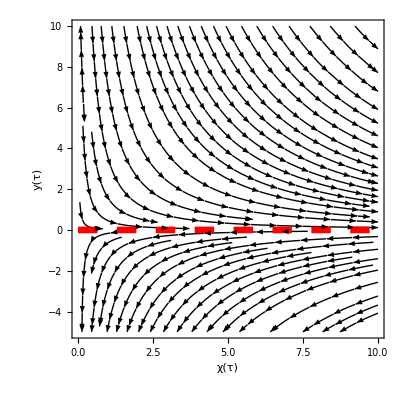

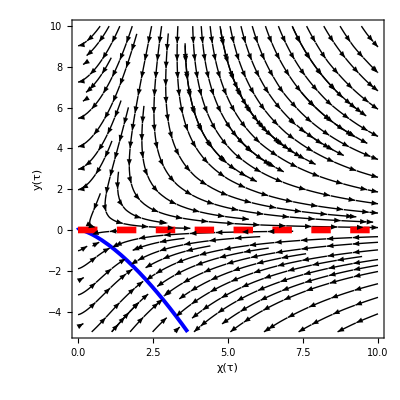

```mathematica
(* critical curve for (g,ζ,σ)=(0,0,0) *)
Hc=Solve[l^2 M-2 κ+M α χ-6 α^3 χ^2+90 M y^2 α^3 χ^2-6 √2 y α √χ (l^2 M-2 κ+2 M α χ)==0,y];

(* Fugue in B flat *)
BbLim={ζ->0,η->0,g->0,σ->0,γ->-α^2};
BbmParam={α->10,M->0,l->10^5,κ->1/2};
BbMParam={α->10,M->10^-8,l->10^5,κ->1/2};

(* set plot range *)
NRange={x0->10^-2,x1->10,y0->-5,y1->10};

(* plots *)
PlotBbm=StreamPlot[{DSχGal[[2]],DSyGal[[2]]}/.{χ[τ]->x,y[τ]->y}/.BbLim/.BbmParam,{x,x0/.NRange,x1/.NRange},{y,y0/.NRange,y1/.NRange},PlotTheme->"Monochrome",AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],FrameLabel->{Style["χ(τ)",FontSize->16],Style["y(τ)",FontSize->16]},RotateLabel->False,PlotRange->{{x0,x1}/.NRange,{y0,y1}/.NRange},PerformanceGoal->"Quality"];
PlotBbM=StreamPlot[{DSχGal[[2]],DSyGal[[2]]}/.{χ[τ]->x,y[τ]->y}/.BbLim/.BbMParam,{x,x0/.NRange,x1/.NRange},{y,y0/.NRange,y1/.NRange},PlotTheme->"Monochrome",AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],FrameLabel->{Style["χ(τ)",FontSize->16],Style["y(τ)",FontSize->16]},RotateLabel->False,PlotRange->{{x0,x1}/.NRange,{y0,y1}/.NRange},PerformanceGoal->"Quality"];

(* Hc, for M≠0 only *)
HcBbM=Plot[{y/.Hc[[1]]/.BbLim/.BbMParam,y/.Hc[[2]]/.BbLim/.BbMParam},{χ,x0/.NRange,x1/.NRange},PlotRange->{{x0,x1}/.NRange,{y0,y1}/.NRange},PlotStyle->{{Blue,Thickness[0.007]},{Blue,Thickness[0.007]}}];

(* well-tempered Minkowski vacuum *)
VacLine=Plot[0,{χ,x0/.NRange,x1/.NRange},PlotStyle->{Red,Dashing[Large],Thickness[0.012]}];

Show[PlotBbm,VacLine]
Show[PlotBbM,HcBbM,VacLine]
```

Now, we consider the following minimal parameters with fixed ζ=σ=g=0 to obtain the Teledeski extended portraits...

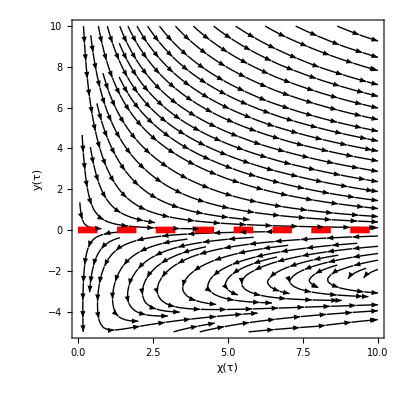

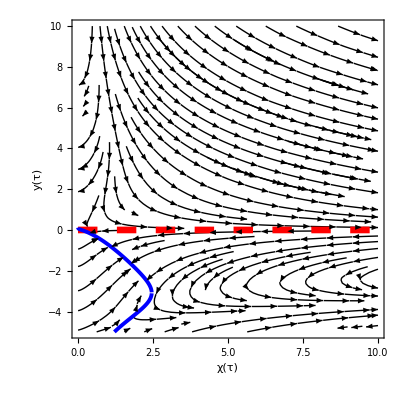

```mathematica
(* Fugue in B flat 7 *)
Bbm7Param={α->10,γ->-1,M->0,ζ->0,σ->10^-4,g->0,l->10^5,η->1,κ->1/2};
BbM7Param={α->10,γ->-1,M->10^-8,ζ->0,σ->10^-4,g->0,l->10^5,η->1,κ->1/2};

(* set plot range *)
NRange={x0->10^-2,x1->10,y0->-5,y1->10};

(* plots *)
PlotBbm7=StreamPlot[{DSχGal[[2]],DSyGal[[2]]}/.{χ[τ]->x,y[τ]->y}/.Bbm7Param,{x,x0/.NRange,x1/.NRange},{y,y0/.NRange,y1/.NRange},PlotTheme->"Monochrome",AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],FrameLabel->{Style["χ(τ)",FontSize->16],Style["y(τ)",FontSize->16]},RotateLabel->False,PlotRange->{{x0,x1}/.NRange,{y0,y1}/.NRange},PerformanceGoal->"Quality"];
PlotBbM7=StreamPlot[{DSχGal[[2]],DSyGal[[2]]}/.{χ[τ]->x,y[τ]->y}/.BbM7Param,{x,x0/.NRange,x1/.NRange},{y,y0/.NRange,y1/.NRange},PlotTheme->"Monochrome",AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],FrameLabel->{Style["χ(τ)",FontSize->16],Style["y(τ)",FontSize->16]},RotateLabel->False,PlotRange->{{x0,x1}/.NRange,{y0,y1}/.NRange},PerformanceGoal->"Quality"];

(* well-tempered Minkowski vacuum *)
VacLine=Plot[0,{χ,x0/.NRange,x1/.NRange},PlotStyle->{Red,Dashing[Large],Thickness[0.012]}];

(* critical curve for ζ = 0 *)
HcBbM7nsol=NSolve[(1/(-1+3 M y^2)√2 (-l^2 M+2 κ+M (-α-216 y^2 σ+108 M y^4 σ) χ+6 √2 M y α^2 χ^(3/2)+72 y^2 (2+M y^2) (α^2+γ) σ χ^2) (-√2 α+12 y α^2 √χ-108 √2 y^4 σ (M-4 (α^2+γ) χ))+12 (α^2 χ+24 √2 y^3 σ √χ (-3 M+4 (α^2+γ) χ))^2)==0/.BbM7Param,y];
HcBbM7=Plot[{y/.HcBbM7nsol[[2]],y/.HcBbM7nsol[[3]]},{χ,x0/.NRange,2.463},PlotRange->{{x0,x1}/.NRange,{y0,y1}/.NRange},PlotStyle->{{Blue,Thickness[0.007]},{Blue,Thickness[0.007]}}];

Show[PlotBbm7,VacLine]
Show[PlotBbM7,VacLine,HcBbM7]
```

Observe the change in the dynamics for y<0 due to the addition of σ>0. Now, we try on the case σ<0. The plots turn out to be...

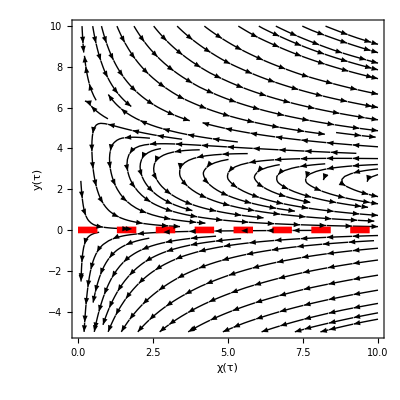

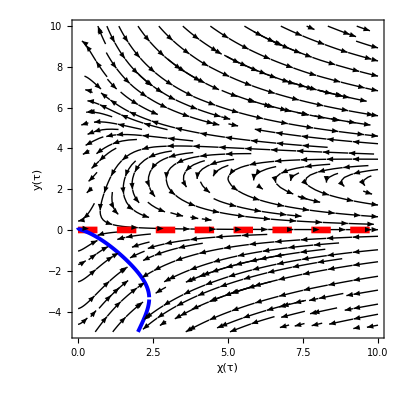

```mathematica
(* Fugue in B flat 7 *)
Bbm7Param={α->10,γ->-1,M->0,ζ->0,σ->-10^-4,g->0,l->10^5,η->1,κ->1/2};
BbM7Param={α->10,γ->-1,M->10^-8,ζ->0,σ->-10^-4,g->0,l->10^5,η->1,κ->1/2};

(* set plot range *)
NRange={x0->10^-2,x1->10,y0->-5,y1->10};

(* plots *)
PlotBbm7=StreamPlot[{DSχGal[[2]],DSyGal[[2]]}/.{χ[τ]->x,y[τ]->y}/.Bbm7Param,{x,x0/.NRange,x1/.NRange},{y,y0/.NRange,y1/.NRange},PlotTheme->"Monochrome",AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],FrameLabel->{Style["χ(τ)",FontSize->16],Style["y(τ)",FontSize->16]},RotateLabel->False,PlotRange->{{x0,x1}/.NRange,{y0,y1}/.NRange},PerformanceGoal->"Quality"];
PlotBbM7=StreamPlot[{DSχGal[[2]],DSyGal[[2]]}/.{χ[τ]->x,y[τ]->y}/.BbM7Param,{x,x0/.NRange,x1/.NRange},{y,y0/.NRange,y1/.NRange},PlotTheme->"Monochrome",AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],FrameLabel->{Style["χ(τ)",FontSize->16],Style["y(τ)",FontSize->16]},RotateLabel->False,PlotRange->{{x0,x1}/.NRange,{y0,y1}/.NRange},PerformanceGoal->"Quality"];

(* well-tempered Minkowski vacuum *)
VacLine=Plot[0,{χ,x0/.NRange,x1/.NRange},PlotStyle->{Red,Dashing[Large],Thickness[0.012]}];

(* critical curve for ζ = 0 *)
HcBbM7nsol=NSolve[(1/(-1+3 M y^2)√2 (-l^2 M+2 κ+M (-α-216 y^2 σ+108 M y^4 σ) χ+6 √2 M y α^2 χ^(3/2)+72 y^2 (2+M y^2) (α^2+γ) σ χ^2) (-√2 α+12 y α^2 √χ-108 √2 y^4 σ (M-4 (α^2+γ) χ))+12 (α^2 χ+24 √2 y^3 σ √χ (-3 M+4 (α^2+γ) χ))^2)==0/.BbM7Param,y];
HcBbM7=Plot[{y/.HcBbM7nsol[[2]],y/.HcBbM7nsol[[3]]},{χ,x0/.NRange,2.38},PlotRange->{{x0,x1}/.NRange,{y0,y1}/.NRange},PlotStyle->{{Blue,Thickness[0.007]},{Blue,Thickness[0.007]}}];

Show[PlotBbm7,VacLine]
Show[PlotBbM7,VacLine,HcBbM7]
```

Clearly, something interesting is happening with σ<0.

#### C. Phase transition

We assess the stability of the vacuum through a phase transition implemented through the effective energy density...

```mathematica
ptρ=ρ->Function[t,ρΛ+(ΔρΛ/2 Tanh[(t-T)/Δt])];
```

...where ρ_Λ is an initial vacuum energy that would be changed by Δρ_Λ in an interval Δt at time t~T.A plot of this  effective energy density and pressure for Δρ_Λ~10^2/L^2 where L is a length scale is shown below...

ρ[τ]==(l^2 (2+Δ Tanh[(τ-Τ)/Δτ]))/(2 L^2)

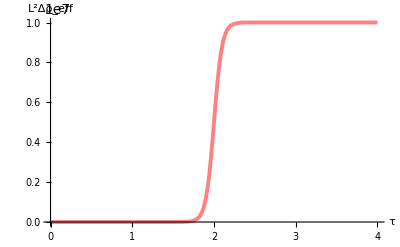

```mathematica
ptNdim={t->L τ,T->L Τ,Δt->L Δτ,ρΛ->l^2/L^2,ΔρΛ->(l^2/L^2)Δ};
ρ[τ]==(ρ[t]/.ptρ/.ptNdim//Simplify)

ρΛnd[τ_]=L^2 ρ[t]/.ptρ/.ptNdim//Simplify;
Plot[{(ρΛnd[τ]-ρΛnd[0])/.Solve[l2i==l^2-(l^2 Δ)/2,l][[2]]/.{l2i->10^10,Δ->10^-3,Τ->2,Δτ->1/10}},{τ,0,4},PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ","L^2Δρ_eff"}]
```

We proceed to use this with the field equations. To prepare the numerical integration, we obtain the Friedmann and scalar field equations...

```mathematica
FeqGalpt=(FeqTH[[1]]/a[t]^3/.FugueBFlatMajor7/.WTCondensate/.β->0//Simplify)/.√(ϕ'[t]^2)->ϕ'[t]/.ptρ//Simplify;
SeqGalpt=(SeqTH[[1]]/a[t]^3/.FugueBFlatMajor7/.WTCondensate/.β->0//Simplify)/.√(ϕ'[t]^2)->ϕ'[t]/.1/(√(ϕ'[t]^2))->ϕ'[t]/.(ϕ'[t]^2)^(3/2)->ϕ'[t]^3//Simplify;

FeqGalpt==0
SeqGalpt==0
```

1/(4 λ^3)(12 (α^2 η+γ (-1+η) λ^3) H[t] ϕ'[t]^3-2 λ^3 (2 ρΛ+ΔρΛ Tanh[(t-T)/Δt]+2 λ^3 ϕ[t]+α ϕ'[t]^2)-72 σ H[t]^4 ϕ'[t] (12 √2 g λ^3+15 M λ^3 ϕ'[t]-7 η (α^2+γ λ^3) ϕ'[t]^3)+3 λ^3 H[t]^2 (8 κ+4 M ϕ[t]-15 ζ ϕ'[t]^4))==0

-1/λ^3 ϕ'[t]^2 (λ^6-3 (α^2 η+γ (-1+η) λ^3) H'[t] ϕ'[t]^2+54 σ H[t]^5 (3 √2 g λ^3+6 M λ^3 ϕ'[t]-4 η (α^2+γ λ^3) ϕ'[t]^3)+9 H[t]^3 (3 ζ λ^3 ϕ'[t]^3+8 σ H'[t] (3 √2 g λ^3+6 M λ^3 ϕ'[t]-4 η (α^2+γ λ^3) ϕ'[t]^3))+α λ^3 ϕ''[t]+108 σ H[t]^4 (M λ^3-2 η (α^2+γ λ^3) ϕ'[t]^2) ϕ''[t]+3 H[t] ϕ'[t] (α λ^3+6 ζ λ^3 H'[t] ϕ'[t]^2-2 (α^2 η+γ (-1+η) λ^3) ϕ''[t])+3 H[t]^2 (M λ^3-3 ϕ'[t]^2 (α^2 η+γ (-1+η) λ^3-3 ζ λ^3 ϕ''[t])))==0

We nondimensionalize these equations as follows...

```mathematica
$Assumptions=L>0;
ndGalParams={λ->1/L^(2/3),γ->L^2 γ,ζ->L^4 ζ,g->g/L,Λ->l^2/L^2,σ->σ L^4};
ndGalFields={H[t]->y[τ]/L,H'[t]->y'[τ]/L^2,ϕ[t]->ψ[τ],ϕ'[t]->ψ'[τ]/L,ϕ''[t]->ψ''[τ]/L^2};

FeqGalptnd=FeqGalpt==0/.ndGalParams/.ndGalFields/.ptNdim//Simplify;
SeqGalptnd=SeqGalpt==0/.ndGalParams/.ndGalFields//Simplify;

FeqGalptnd
SeqGalptnd
```

2 (l^2 (2+Δ Tanh[(τ-Τ)/Δτ])+2 ψ[τ]+α ψ'[τ]^2+36 σ y[τ]^4 ψ'[τ] (12 √2 g+15 M ψ'[τ]-7 (α^2+γ) η ψ'[τ]^3))==3 y[τ] (4 (γ (-1+η)+α^2 η) ψ'[τ]^3+y[τ] (8 κ+4 M ψ[τ]-15 ζ ψ'[τ]^4))

ψ'[τ] (-1+3 (γ (-1+η)+α^2 η) y'[τ] ψ'[τ]^2-54 σ y[τ]^5 (3 √2 g+6 M ψ'[τ]-4 (α^2+γ) η ψ'[τ]^3)-9 y[τ]^3 (3 ζ ψ'[τ]^3+8 σ y'[τ] (3 √2 g+6 M ψ'[τ]-4 (α^2+γ) η ψ'[τ]^3))-α ψ''[τ]-108 σ y[τ]^4 (M-2 (α^2+γ) η ψ'[τ]^2) ψ''[τ]-3 y[τ] ψ'[τ] (α+6 ζ y'[τ] ψ'[τ]^2-2 (γ (-1+η)+α^2 η) ψ''[τ])-3 y[τ]^2 (M-3 ψ'[τ]^2 (γ (-1+η)+α^2 η-3 ζ ψ''[τ])))==0

We fix the initial parameters (ψ_0',y_0) on the Hamiltonian constraint through the equation...

```mathematica
InitHSurfacept=FeqGalptnd/.{y[τ]->y0,ψ[τ]->ψ0,ψ'[τ]->ψp0}/.τ->τ0//Simplify;

ψ0Initpt=Solve[InitHSurfacept,ψ0][[1]];
"ψ_0"==(ψ0/.ψ0Initpt)
```

ψ_0==-1/(4 (-1+3 M y0^2))(-4 l^2+24 y0^2 κ-864 √2 g y0^4 σ ψp0-2 α ψp0^2-1080 M y0^4 σ ψp0^2-12 y0 γ ψp0^3+12 y0 α^2 η ψp0^3+12 y0 γ η ψp0^3-45 y0^2 ζ ψp0^4+504 y0^4 α^2 η σ ψp0^4+504 y0^4 γ η σ ψp0^4-2 l^2 Δ Tanh[(-Τ+τ0)/Δτ])

Moving on the the integration, we prepare the dynamical equations...

```mathematica
eq1pt=(D[(FeqGalptnd[[1]]-FeqGalptnd[[2]]), τ]//Simplify)==0;
eq2pt=SeqGalptnd;
```

So, here’s a test run...

```mathematica
(* Fugue in B flat 7 *)
Bbm7Param={α->10,γ->-1,M->0,ζ->0,σ->10^-4,g->0,η->1,κ->1/2};
BbM7Param={α->10,γ->-1,M->10^-8,ζ->0,σ->10^-4,g->0,η->1,κ->1/2};

(* l2i = initial vacuum energy *)
lTol2i=Solve[l2i==l^2-(l^2 Δ)/2,l][[2]];

(* phase transition parameters*)
ptParam={l2i->10^10,Δ->10^-3,Τ->2,Δτ->1/10};

(* initial conditions *)
τparam={τ0->10^-5,τf->10^5};
Init={y0->10^-3,ψp0->1};

(* here we go, numerical integration *)
solptBbm7=NDSolve[{eq1pt,eq2pt,y[τ0]==y0,ψ[τ0]==(ψ0/.ψ0Initpt),ψ'[τ0]==ψp0}/.lTol2i/.Bbm7Param/.ptParam/.τparam/.Init,{y,ψ},{τ,τ0,τf}/.τparam,PrecisionGoal->20,AccuracyGoal->20,WorkingPrecision->60][[1]];
solptBbM7=NDSolve[{eq1pt,eq2pt,y[τ0]==y0,ψ[τ0]==(ψ0/.ψ0Initpt),ψ'[τ0]==ψp0}/.lTol2i/.BbM7Param/.ptParam/.τparam/.Init,{y,ψ},{τ,τ0,τf}/.τparam,PrecisionGoal->20,AccuracyGoal->20,WorkingPrecision->60][[1]];
```

So here are the plots superposing the B Flat extension cases...

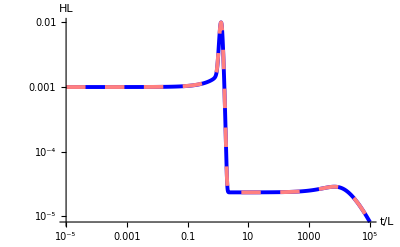

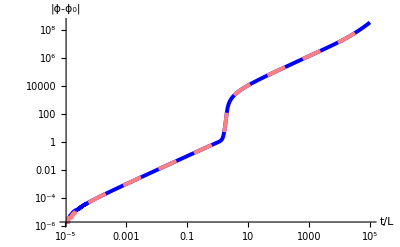

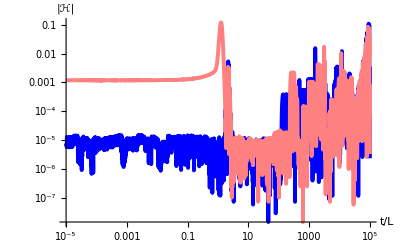

```mathematica
(* Hubble function *)
HBb7Inset=LogLogPlot[Abs[(y[τ]/.solptBbm7)-(y[τ]/.solptBbM7)],{τ,τ0/.τparam,τf/.τparam},PlotRange->All,AxesStyle->Directive[Black,10],LabelStyle->Directive[Black,10],Ticks->Automatic,TicksStyle->Directive[Black,10],PlotStyle->{{Red,Thickness[0.02]}},AxesLabel->{"t/L","|(H_(M=0)-H_(M≠0))L|"}];
LogLogPlot[{y[τ]/.solptBbm7,y[τ]/.solptBbM7},{τ,τ0/.τparam,τf/.τparam},PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]},{Pink,Dashing[Large],Thickness[0.007]}},AxesLabel->{"t/L","HL"},Epilog->Inset[HBb7Inset,{Log[5 10^-3],Log[0.6 10^-4]},Automatic,Scaled[0.5]]]

(* scalar field *)
ϕBb7Inset=LogLogPlot[(ψ[τ]/.solptBbm7)-(ψ[τ]/.solptBbM7),{τ,τ0/.τparam,τf/.τparam},PlotRange->All,AxesStyle->Directive[Black,10],LabelStyle->Directive[Black,10],Ticks->Automatic,TicksStyle->Directive[Black,10],PlotStyle->{{Red,Thickness[0.02]}},AxesLabel->{"t/L","|ϕ_(M=0)-ϕ_(M≠0)|"}];
LogLogPlot[{ψ[τ]-ψ0/.ψ0Initpt/.lTol2i/.Bbm7Param/.ptParam/.τparam/.Init/.solptBbm7,ψ[τ]-ψ0/.ψ0Initpt/.lTol2i/.BbM7Param/.ptParam/.τparam/.Init/.solptBbM7},{τ,τ0/.τparam,τf/.τparam},PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]},{Pink,Dashing[Large],Thickness[0.007]}},AxesLabel->{"t/L","|ϕ-ϕ_0|"},Epilog->Inset[ϕBb7Inset,{Log[1/2 10^-2],Log[10^5]},Automatic,Scaled[0.5]]]

(* Hamiltonian constraint *)
LogLogPlot[{Abs[FeqGalptnd[[1]]-FeqGalptnd[[2]]]/.ψ0Initpt/.lTol2i/.Bbm7Param/.ptParam/.τparam/.Init/.solptBbm7,Abs[FeqGalptnd[[1]]-FeqGalptnd[[2]]]/.ψ0Initpt/.lTol2i/.Bbm7Param/.ptParam/.τparam/.Init/.solptBbM7},{τ,τ0/.τparam,τf/.τparam},PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]},{Pink,Thickness[0.007]}},AxesLabel->{"t/L","|ℋ|"}]
```

For a different set of initial conditions (-ϕ̇>>1) and phase transition, we can avoid the loitering quasi de Sitter phases...

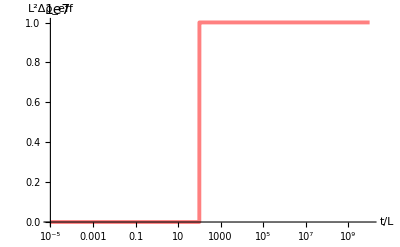

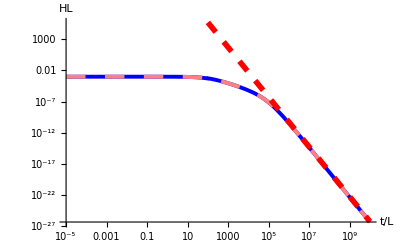

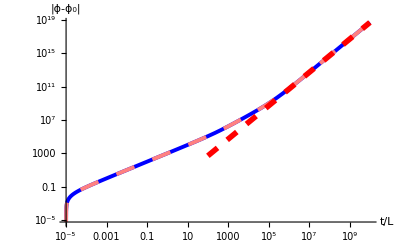

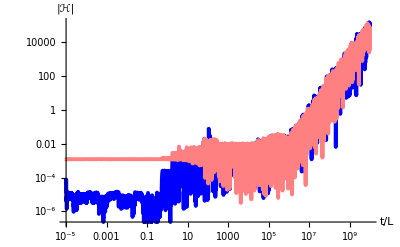

```mathematica
(* phase transition parameters*)
ptParam={l2i->10^10,Δ->10^-3,Τ->10^2,Δτ->1/10};

(* initial conditions *)
τparam={τ0->10^-5,τf->10^10};
Init={y0->10^-3,ψp0->-10^3};

(* here we go, numerical integration *)
solptBbm7=NDSolve[{eq1pt,eq2pt,y[τ0]==y0,ψ[τ0]==(ψ0/.ψ0Initpt),ψ'[τ0]==ψp0}/.lTol2i/.Bbm7Param/.ptParam/.τparam/.Init,{y,ψ},{τ,τ0,τf}/.τparam,PrecisionGoal->20,AccuracyGoal->20,WorkingPrecision->50][[1]];
solptBbM7=NDSolve[{eq1pt,eq2pt,y[τ0]==y0,ψ[τ0]==(ψ0/.ψ0Initpt),ψ'[τ0]==ψp0}/.lTol2i/.BbM7Param/.ptParam/.τparam/.Init,{y,ψ},{τ,τ0,τf}/.τparam,PrecisionGoal->20,AccuracyGoal->20,WorkingPrecision->50][[1]];

(* phase transition *)
LogLinearPlot[{(ρΛnd[τ]-ρΛnd[0])/.lTol2i/.ptParam},{τ,τ0/.τparam,τf/.τparam},PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"t/L","L^2Δρ_eff"}]

(* Hubble function *)
HBb7Inset=LogLogPlot[Abs[(y[τ]/.solptBbm7)-(y[τ]/.solptBbM7)],{τ,τ0/.τparam,τf/.τparam},PlotRange->All,AxesStyle->Directive[Black,10],LabelStyle->Directive[Black,10],Ticks->Automatic,TicksStyle->Directive[Black,10],PlotStyle->{{Red,Thickness[0.02]}},AxesLabel->{"t/L","|(H_(M=0)-H_(M≠0))L|"}];
HBb7Asymp=LogLogPlot[δC[1]/((-6 α^3+3 ζ ) τ^4)/.δC[1]->-10^17.5/.Bbm7Param,{τ,10^2,τf/.τparam},PlotRange->All,PlotStyle->{Red,Dashing[Medium],Thickness[0.01]}];
HBb7Plot=LogLogPlot[{y[τ]/.solptBbm7,y[τ]/.solptBbM7},{τ,τ0/.τparam,τf/.τparam},PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]},{Pink,Dashing[Large],Thickness[0.007]}},AxesLabel->{"t/L","HL"},Epilog->Inset[HBb7Inset,{Log[5 10^-1],Log[10^-17]},Automatic,Scaled[0.5]]];
Show[HBb7Plot,HBb7Asymp]

(* scalar field *)
ϕBb7Inset=LogLogPlot[Abs[(ψ[τ]/.solptBbm7)-(ψ[τ]/.solptBbM7)],{τ,τ0/.τparam,τf/.τparam},PlotRange->All,AxesStyle->Directive[Black,10],LabelStyle->Directive[Black,10],Ticks->Automatic,TicksStyle->Directive[Black,10],PlotStyle->{{Red,Thickness[0.02]}},AxesLabel->{"t/L","|ϕ_(M=0)-ϕ_(M≠0)|"}];
ϕBb7Asymp=LogLogPlot[τ^2/(2α)/.Bbm7Param,{τ,10^2,τf/.τparam},PlotRange->All,PlotStyle->{Red,Dashing[Medium],Thickness[0.01]}];
ϕBb7Plot=LogLogPlot[{-(ψ[τ]-ψ0)/.ψ0Initpt/.lTol2i/.Bbm7Param/.ptParam/.τparam/.Init/.solptBbm7,-(ψ[τ]-ψ0)/.ψ0Initpt/.lTol2i/.BbM7Param/.ptParam/.τparam/.Init/.solptBbM7},{τ,τ0/.τparam,τf/.τparam},PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]},{Pink,Dashing[Large],Thickness[0.007]}},AxesLabel->{"t/L","|ϕ-ϕ_0|"},Epilog->Inset[ϕBb7Inset,{Log[5 10^-1],Log[1/2 10^14]},Automatic,Scaled[0.5]]];
Show[ϕBb7Plot,ϕBb7Asymp]

(* Hamiltonian constraint *)
LogLogPlot[{Abs[FeqGalptnd[[1]]-FeqGalptnd[[2]]]/.ψ0Initpt/.lTol2i/.Bbm7Param/.ptParam/.τparam/.Init/.solptBbm7,Abs[FeqGalptnd[[1]]-FeqGalptnd[[2]]]/.ψ0Initpt/.lTol2i/.Bbm7Param/.ptParam/.τparam/.Init/.solptBbM7},{τ,τ0/.τparam,τf/.τparam},PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]},{Pink,Thickness[0.007]}},AxesLabel->{"t/L","|ℋ|"}]
```

Here is a zoom in of the response of the Hubble function to the phase transition...

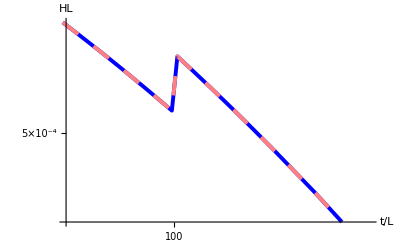

```mathematica
LogLogPlot[{y[τ]/.solptBbm7,y[τ]/.solptBbM7},{τ,τ0/.τparam,τf/.τparam},PlotRange->{{8/10 10^2,3/2 10^2},{4.5 10^-4,5.7 10^-4}},AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]},{Pink,Dashing[Large],Thickness[0.007]}},AxesLabel->{"t/L","HL"}]
```